# INTSECA

This notebook contains details of using twisted intersection theory to generate the master integrals and the associated canonical system for the three-site chain.

```mathematica
SetDirectory[NotebookDirectory[]];
<<INTSECA.wl
```

INTSECA 1.2.0

Union::normal: Nonatomic expression expected at position 1 in Union[Global`powers].

## 4-site chain

### Definitions

```mathematica
dim=4;
nkin=7;
kin={X1,X2,X3,X4,Y12,Y23,Y34};
```

Untwisted hyperplanes:

```mathematica
nBplane=10;
B[1]={1,0,0,0,X1+Y12};
B[2]={0,1,0,0,X2+Y12+Y23};
B[3]={0,0,1,0,X3+Y23+Y34};
B[4]={0,0,0,1,X4+Y34};
B[5]={1,1,1,1,X1+X2+X3+X4};
B[6]={1,1,0,0,X1+X2+Y23};
B[7]={0,1,1,0,X2+X3+Y12+Y34};
B[8]={0,0,1,1,X3+X4+Y23};
B[9]={1,1,1,0,X1+X2+X3+Y34};
B[10]={0,1,1,1,X2+X3+X4+Y12};
```

Twisted hyperplanes:

```mathematica
nTplane=4;
T[1]={1,0,0,0,0}; 
T[2]={0,1,0,0,0}; 
T[3]={0,0,1,0,0}; 
T[4]={0,0,0,1,0}; 
powers={e,e,e,e};
```

Wavefunction:

```mathematica
(*need to break the 1/(...) to dlog-forms*)
```

```mathematica
psi=-⟨1,2,3,4⟩+⟨1,2,3,8⟩-⟨1,2,4,7⟩-⟨1,2,4,8⟩+⟨1,2,4,10⟩-⟨1,2,7,10⟩+⟨1,3,4,6⟩+⟨1,3,4,7⟩-⟨1,3,4,9⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,3,6,8⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩-⟨1,4,5,6⟩+⟨1,4,5,8⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩+⟨1,4,8,10⟩+⟨1,5,6,9⟩-⟨2,3,4,6⟩-⟨2,3,6,8⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,8⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨3,4,7,9⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨4,5,8,10⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

451

```mathematica
sol=Sol[]
```

{⟨1,2,3,14⟩→0,⟨1,2,4,13⟩→0,⟨1,2,5,14⟩→-⟨1,2,5,13⟩,⟨1,2,7,14⟩→0,⟨1,2,8,14⟩→-⟨1,2,8,13⟩,⟨1,2,9,14⟩→0,⟨1,2,10,14⟩→-⟨1,2,10,13⟩,⟨1,2,13,14⟩→0,⟨1,3,4,12⟩→0,⟨1,3,5,14⟩→-⟨1,3,5,12⟩,⟨1,3,6,14⟩→0,⟨1,3,7,14⟩→0,⟨1,3,8,12⟩→0,⟨1,3,9,14⟩→0,⟨1,3,10,14⟩→-⟨1,3,10,12⟩,⟨1,3,12,14⟩→0,⟨1,4,5,13⟩→-⟨1,4,5,12⟩,⟨1,4,6,13⟩→0,⟨1,4,7,13⟩→-⟨1,4,7,12⟩,⟨1,4,8,12⟩→0,⟨1,4,9,13⟩→-⟨1,4,9,12⟩,⟨1,4,10,13⟩→-⟨1,4,10,12⟩,⟨1,4,12,13⟩→0,⟨1,5,6,14⟩→-⟨1,5,6,13⟩,⟨1,5,7,13⟩→-⟨1,5,7,12⟩,⟨1,5,8,9⟩→-⟨1,3,5,8⟩-⟨1,3,5,9⟩-⟨1,3,8,9⟩,⟨1,5,8,14⟩→-⟨1,5,8,13⟩,⟨1,5,9,13⟩→-⟨1,5,9,12⟩,⟨1,5,12,14⟩→-⟨1,5,12,13⟩,⟨1,5,13,14⟩→⟨1,5,12,13⟩,⟨1,6,7,14⟩→0,⟨1,6,8,14⟩→-⟨1,6,8,13⟩,⟨1,6,9,14⟩→0,⟨1,6,10,14⟩→-⟨1,6,10,13⟩,⟨1,6,13,14⟩→0,⟨1,7,8,10⟩→-⟨1,3,7,8⟩-⟨1,3,7,10⟩-⟨1,3,8,10⟩,⟨1,7,8,14⟩→-⟨1,7,8,12⟩-⟨1,7,8,13⟩,⟨1,7,10,13⟩→-⟨1,7,10,12⟩,⟨1,7,12,14⟩→0,⟨1,7,13,14⟩→0,⟨1,8,9,14⟩→-⟨1,8,9,12⟩-⟨1,8,9,13⟩,⟨1,8,10,14⟩→-⟨1,8,10,13⟩,⟨1,8,12,13⟩→0,⟨1,8,12,14⟩→0,⟨1,9,10,13⟩→-⟨1,9,10,12⟩,⟨1,9,12,14⟩→0,⟨1,9,13,14⟩→0,⟨1,10,12,14⟩→-⟨1,10,12,13⟩,⟨1,10,13,14⟩→⟨1,10,12,13⟩,⟨1,12,13,14⟩→0,⟨2,3,4,11⟩→0,⟨2,3,5,14⟩→-⟨2,3,5,11⟩,⟨2,3,6,14⟩→0,⟨2,3,8,11⟩→0,⟨2,3,9,14⟩→0,⟨2,3,10,11⟩→0,⟨2,3,11,14⟩→0,⟨2,4,5,13⟩→-⟨2,4,5,11⟩,⟨2,4,6,13⟩→0,⟨2,4,7,11⟩→0,⟨2,4,8,11⟩→0,⟨2,4,9,13⟩→-⟨2,4,9,11⟩,⟨2,4,10,11⟩→0,⟨2,4,11,13⟩→0,⟨2,5,6,14⟩→-⟨2,5,6,13⟩,⟨2,5,7,14⟩→-⟨2,5,7,11⟩,⟨2,5,8,9⟩→-⟨2,3,5,8⟩-⟨2,3,5,9⟩-⟨2,3,8,9⟩,⟨2,5,8,14⟩→-⟨2,5,8,13⟩,⟨2,5,9,13⟩→-⟨2,5,9,11⟩,⟨2,5,10,14⟩→-⟨2,5,10,13⟩,⟨2,5,11,14⟩→-⟨2,5,11,13⟩,⟨2,5,13,14⟩→⟨2,5,11,13⟩,⟨2,6,7,14⟩→0,⟨2,6,8,14⟩→-⟨2,6,8,13⟩,⟨2,6,9,14⟩→0,⟨2,6,10,14⟩→-⟨2,6,10,13⟩,⟨2,6,13,14⟩→0,⟨2,7,8,11⟩→0,⟨2,7,9,14⟩→0,⟨2,7,10,11⟩→0,⟨2,7,11,14⟩→0,⟨2,8,9,14⟩→-⟨2,8,9,11⟩-⟨2,8,9,13⟩,⟨2,8,11,13⟩→0,⟨2,8,11,14⟩→0,⟨2,9,10,14⟩→-⟨2,9,10,11⟩-⟨2,9,10,13⟩,⟨2,9,11,14⟩→0,⟨2,9,13,14⟩→0,⟨2,10,11,13⟩→0,⟨2,10,11,14⟩→0,⟨2,11,13,14⟩→0,⟨3,4,5,12⟩→-⟨3,4,5,11⟩,⟨3,4,6,12⟩→-⟨3,4,6,11⟩,⟨3,4,7,11⟩→0,⟨3,4,9,12⟩→-⟨3,4,9,11⟩,⟨3,4,10,11⟩→0,⟨3,4,11,12⟩→0,⟨3,5,6,10⟩→-⟨2,3,5,6⟩-⟨2,3,5,10⟩-⟨2,3,6,10⟩,⟨3,5,6,12⟩→-⟨3,5,6,11⟩,⟨3,5,7,14⟩→-⟨3,5,7,11⟩,⟨3,5,8,12⟩→-⟨3,5,8,11⟩,⟨3,5,9,12⟩→-⟨3,5,9,11⟩,⟨3,5,10,14⟩→-⟨3,5,10,12⟩,⟨3,5,11,14⟩→-⟨3,5,11,12⟩,⟨3,5,12,14⟩→⟨3,5,11,12⟩,⟨3,6,7,14⟩→0,⟨3,6,8,12⟩→-⟨3,6,8,11⟩,⟨3,6,10,14⟩→-⟨3,6,10,11⟩-⟨3,6,10,12⟩,⟨3,6,11,14⟩→0,⟨3,6,12,14⟩→0,⟨3,7,8,11⟩→0,⟨3,7,9,14⟩→0,⟨3,7,10,11⟩→0,⟨3,7,11,14⟩→0,⟨3,8,9,12⟩→-⟨3,8,9,11⟩,⟨3,8,10,11⟩→0,⟨3,8,11,12⟩→0,⟨3,9,10,14⟩→-⟨3,9,10,11⟩-⟨3,9,10,12⟩,⟨3,9,11,14⟩→0,⟨3,9,12,14⟩→0,⟨3,10,11,12⟩→0,⟨3,10,11,14⟩→0,⟨3,11,12,14⟩→0,⟨4,5,6,10⟩→-⟨2,4,5,6⟩-⟨2,4,5,10⟩-⟨2,4,6,10⟩,⟨4,5,6,12⟩→-⟨4,5,6,11⟩,⟨4,5,7,13⟩→-⟨4,5,7,12⟩,⟨4,5,8,12⟩→-⟨4,5,8,11⟩,⟨4,5,10,13⟩→-⟨4,5,10,12⟩,⟨4,5,11,13⟩→-⟨4,5,11,12⟩,⟨4,5,12,13⟩→⟨4,5,11,12⟩,⟨4,6,7,9⟩→-⟨2,4,6,7⟩-⟨2,4,6,9⟩-⟨2,4,7,9⟩,⟨4,6,7,13⟩→-⟨4,6,7,11⟩-⟨4,6,7,12⟩,⟨4,6,8,12⟩→-⟨4,6,8,11⟩,⟨4,6,9,12⟩→-⟨4,6,9,11⟩,⟨4,6,10,13⟩→-⟨4,6,10,11⟩-⟨4,6,10,12⟩,⟨4,6,11,13⟩→0,⟨4,6,12,13⟩→0,⟨4,7,8,11⟩→0,⟨4,7,9,13⟩→-⟨4,7,9,12⟩,⟨4,7,11,12⟩→0,⟨4,7,11,13⟩→0,⟨4,8,9,12⟩→-⟨4,8,9,11⟩,⟨4,8,10,11⟩→0,⟨4,8,11,12⟩→0,⟨4,9,10,13⟩→-⟨4,9,10,12⟩,⟨4,9,11,13⟩→-⟨4,9,11,12⟩,⟨4,9,12,13⟩→⟨4,9,11,12⟩,⟨4,10,11,12⟩→0,⟨4,10,11,13⟩→0,⟨4,11,12,13⟩→0,⟨5,6,7,14⟩→-⟨5,6,7,11⟩-⟨5,6,7,12⟩-⟨5,6,7,13⟩,⟨5,6,9,12⟩→-⟨5,6,9,11⟩,⟨5,6,10,13⟩→-⟨2,5,6,13⟩-⟨2,5,10,13⟩-⟨2,6,10,13⟩,⟨5,6,10,14⟩→⟨2,5,6,13⟩+⟨2,5,10,13⟩+⟨2,6,10,13⟩,⟨5,6,11,14⟩→-⟨5,6,11,13⟩,⟨5,6,12,13⟩→-⟨5,6,11,13⟩,⟨5,6,12,14⟩→⟨5,6,11,13⟩,⟨5,7,8,14⟩→-⟨5,7,8,11⟩-⟨5,7,8,12⟩-⟨5,7,8,13⟩,⟨5,7,9,13⟩→-⟨5,7,9,12⟩,⟨5,7,10,13⟩→-⟨5,7,10,12⟩,⟨5,7,11,13⟩→-⟨5,7,11,12⟩,⟨5,7,12,14⟩→⟨5,7,11,12⟩,⟨5,7,13,14⟩→-⟨5,7,11,12⟩,⟨5,8,9,11⟩→-⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨3,8,9,11⟩,⟨5,8,9,12⟩→⟨3,5,8,11⟩+⟨3,5,9,11⟩+⟨3,8,9,11⟩,⟨5,8,10,14⟩→-⟨5,8,10,13⟩,⟨5,8,11,14⟩→-⟨5,8,11,13⟩,⟨5,8,12,13⟩→-⟨5,8,11,13⟩,⟨5,8,12,14⟩→⟨5,8,11,13⟩,⟨5,9,10,13⟩→-⟨5,9,10,12⟩,⟨5,9,11,13⟩→-⟨5,9,11,12⟩,⟨5,9,12,13⟩→⟨5,9,11,12⟩,⟨5,10,12,14⟩→-⟨5,10,12,13⟩,⟨5,10,13,14⟩→⟨5,10,12,13⟩,⟨5,11,12,14⟩→-⟨5,11,12,13⟩,⟨5,11,13,14⟩→⟨5,11,12,13⟩,⟨5,12,13,14⟩→-⟨5,11,12,13⟩,⟨6,7,8,9⟩→-⟨2,6,7,8⟩-⟨2,6,8,9⟩-⟨2,7,8,9⟩,⟨6,7,8,10⟩→-⟨3,6,7,8⟩-⟨3,6,7,10⟩-⟨3,6,8,10⟩,⟨6,7,8,14⟩→-⟨6,7,8,11⟩-⟨6,7,8,12⟩-⟨6,7,8,13⟩,⟨6,7,9,10⟩→-⟨2,5,6,7⟩-⟨2,5,6,9⟩-⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,9,10⟩-⟨2,6,7,10⟩-⟨2,6,9,10⟩-⟨2,7,9,10⟩-⟨5,6,7,9⟩-⟨5,6,7,10⟩-⟨5,6,9,10⟩,⟨6,7,9,14⟩→0,⟨6,7,10,13⟩→-⟨6,7,10,11⟩-⟨6,7,10,12⟩,⟨6,7,11,14⟩→0,⟨6,7,12,14⟩→0,⟨6,7,13,14⟩→0,⟨6,8,9,12⟩→-⟨6,8,9,11⟩,⟨6,8,10,14⟩→-⟨6,8,10,13⟩,⟨6,8,11,14⟩→-⟨6,8,11,13⟩,⟨6,8,12,13⟩→-⟨6,8,11,13⟩,⟨6,8,12,14⟩→⟨6,8,11,13⟩,⟨6,9,10,14⟩→-⟨6,9,10,11⟩-⟨6,9,10,12⟩,⟨6,9,11,14⟩→0,⟨6,9,12,14⟩→0,⟨6,10,11,14⟩→-⟨6,10,11,13⟩,⟨6,10,12,14⟩→-⟨6,10,12,13⟩,⟨6,10,13,14⟩→⟨6,10,11,13⟩+⟨6,10,12,13⟩,⟨6,11,13,14⟩→0,⟨6,12,13,14⟩→0,⟨7,8,9,10⟩→-⟨3,5,7,8⟩-⟨3,5,7,9⟩-⟨3,5,7,10⟩-⟨3,5,8,10⟩-⟨3,5,9,10⟩-⟨3,7,8,9⟩-⟨3,7,9,10⟩-⟨3,8,9,10⟩-⟨5,7,8,9⟩-⟨5,7,8,10⟩-⟨5,8,9,10⟩,⟨7,8,9,14⟩→-⟨7,8,9,12⟩-⟨7,8,9,13⟩,⟨7,8,10,11⟩→0,⟨7,8,11,12⟩→0,⟨7,8,11,13⟩→0,⟨7,8,11,14⟩→0,⟨7,9,10,12⟩→-⟨5,7,9,12⟩-⟨5,7,10,12⟩-⟨5,9,10,12⟩,⟨7,9,10,13⟩→⟨5,7,9,12⟩+⟨5,7,10,12⟩+⟨5,9,10,12⟩,⟨7,9,12,14⟩→0,⟨7,9,13,14⟩→0,⟨7,10,11,12⟩→0,⟨7,10,11,13⟩→0,⟨7,11,12,14⟩→0,⟨7,11,13,14⟩→0,⟨8,9,10,14⟩→-⟨8,9,10,11⟩-⟨8,9,10,13⟩,⟨8,9,11,14⟩→-⟨8,9,11,12⟩-⟨8,9,11,13⟩,⟨8,9,12,13⟩→-⟨8,9,11,13⟩,⟨8,9,12,14⟩→⟨8,9,11,12⟩+⟨8,9,11,13⟩,⟨8,10,11,13⟩→0,⟨8,10,11,14⟩→0,⟨8,11,12,13⟩→0,⟨8,11,12,14⟩→0,⟨9,10,11,13⟩→-⟨9,10,11,12⟩,⟨9,10,12,14⟩→⟨9,10,11,12⟩-⟨9,10,12,13⟩,⟨9,10,13,14⟩→-⟨9,10,11,12⟩+⟨9,10,12,13⟩,⟨9,11,12,14⟩→0,⟨9,11,13,14⟩→0,⟨9,12,13,14⟩→0,⟨10,11,12,13⟩→0,⟨10,11,12,14⟩→0,⟨10,11,13,14⟩→0,⟨11,12,13,14⟩→0}

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({5} | {⟨5,11,12,13⟩}
{1,5} | {⟨1,5,12,13⟩}
{1,10} | {⟨1,10,12,13⟩}
{2,5} | {⟨2,5,11,13⟩}
{3,5} | {⟨3,5,11,12⟩}
{4,5} | {⟨4,5,11,12⟩}
{4,9} | {⟨4,9,11,12⟩}
{5,6} | {⟨5,6,11,13⟩}
{5,7} | {⟨5,7,11,12⟩}
{5,8} | {⟨5,8,11,13⟩}
{5,9} | {⟨5,9,11,12⟩}
{5,10} | {⟨5,10,12,13⟩}
{6,8} | {⟨6,8,11,13⟩}
{6,10} | {⟨6,10,11,13⟩,⟨6,10,12,13⟩}
{8,9} | {⟨8,9,11,12⟩,⟨8,9,11,13⟩}
{9,10} | {⟨9,10,11,12⟩,⟨9,10,12,13⟩}
{1,2,5} | {⟨1,2,5,13⟩}
{1,2,8} | {⟨1,2,8,13⟩}
{1,2,10} | {⟨1,2,10,13⟩}
{1,3,5} | {⟨1,3,5,12⟩}
{1,3,10} | {⟨1,3,10,12⟩}
{1,4,5} | {⟨1,4,5,12⟩}
{1,4,7} | {⟨1,4,7,12⟩}
{1,4,9} | {⟨1,4,9,12⟩}
{1,4,10} | {⟨1,4,10,12⟩}
{1,5,6} | {⟨1,5,6,13⟩}
{1,5,7} | {⟨1,5,7,12⟩}
{1,5,8} | {⟨1,5,8,13⟩}
{1,5,9} | {⟨1,5,9,12⟩}
{1,6,8} | {⟨1,6,8,13⟩}
{1,6,10} | {⟨1,6,10,13⟩}
{1,7,8} | {⟨1,7,8,12⟩,⟨1,7,8,13⟩}
{1,7,10} | {⟨1,7,10,12⟩}
{1,8,9} | {⟨1,8,9,12⟩,⟨1,8,9,13⟩}
{1,8,10} | {⟨1,8,10,13⟩}
{1,9,10} | {⟨1,9,10,12⟩}
{2,3,5} | {⟨2,3,5,11⟩}
{2,4,5} | {⟨2,4,5,11⟩}
{2,4,9} | {⟨2,4,9,11⟩}
{2,5,6} | {⟨2,5,6,13⟩}
{2,5,7} | {⟨2,5,7,11⟩}
{2,5,8} | {⟨2,5,8,13⟩}
{2,5,9} | {⟨2,5,9,11⟩}
{2,5,10} | {⟨2,5,10,13⟩}
{2,6,8} | {⟨2,6,8,13⟩}
{2,6,10} | {⟨2,6,10,13⟩}
{2,8,9} | {⟨2,8,9,11⟩,⟨2,8,9,13⟩}
{2,9,10} | {⟨2,9,10,11⟩,⟨2,9,10,13⟩}
{3,4,5} | {⟨3,4,5,11⟩}
{3,4,6} | {⟨3,4,6,11⟩}
{3,4,9} | {⟨3,4,9,11⟩}
{3,5,6} | {⟨3,5,6,11⟩}
{3,5,7} | {⟨3,5,7,11⟩}
{3,5,8} | {⟨3,5,8,11⟩}
{3,5,9} | {⟨3,5,9,11⟩}
{3,5,10} | {⟨3,5,10,12⟩}
{3,6,8} | {⟨3,6,8,11⟩}
{3,6,10} | {⟨3,6,10,11⟩,⟨3,6,10,12⟩}
{3,8,9} | {⟨3,8,9,11⟩}
{3,9,10} | {⟨3,9,10,11⟩,⟨3,9,10,12⟩}
{4,5,6} | {⟨4,5,6,11⟩}
{4,5,7} | {⟨4,5,7,12⟩}
{4,5,8} | {⟨4,5,8,11⟩}
{4,5,10} | {⟨4,5,10,12⟩}
{4,6,7} | {⟨4,6,7,11⟩,⟨4,6,7,12⟩}
{4,6,8} | {⟨4,6,8,11⟩}
{4,6,9} | {⟨4,6,9,11⟩}
{4,6,10} | {⟨4,6,10,11⟩,⟨4,6,10,12⟩}
{4,7,9} | {⟨4,7,9,12⟩}
{4,8,9} | {⟨4,8,9,11⟩}
{4,9,10} | {⟨4,9,10,12⟩}
{5,6,7} | {⟨5,6,7,11⟩,⟨5,6,7,12⟩,⟨5,6,7,13⟩}
{5,6,9} | {⟨5,6,9,11⟩}
{5,6,10} | {⟨5,6,10,13⟩}
{5,7,8} | {⟨5,7,8,11⟩,⟨5,7,8,12⟩,⟨5,7,8,13⟩}
{5,7,9} | {⟨5,7,9,12⟩}
{5,7,10} | {⟨5,7,10,12⟩}
{5,8,9} | {⟨5,8,9,11⟩}
{5,8,10} | {⟨5,8,10,13⟩}
{5,9,10} | {⟨5,9,10,12⟩}
{6,7,8} | {⟨6,7,8,11⟩,⟨6,7,8,12⟩,⟨6,7,8,13⟩}
{6,7,10} | {⟨6,7,10,11⟩,⟨6,7,10,12⟩}
{6,8,9} | {⟨6,8,9,11⟩}
{6,8,10} | {⟨6,8,10,13⟩}
{6,9,10} | {⟨6,9,10,11⟩,⟨6,9,10,12⟩}
{7,8,9} | {⟨7,8,9,12⟩,⟨7,8,9,13⟩}
{7,9,10} | {⟨7,9,10,12⟩}
{8,9,10} | {⟨8,9,10,11⟩,⟨8,9,10,13⟩}
{1,2,3,4} | {⟨1,2,3,4⟩}
{1,2,3,5} | {⟨1,2,3,5⟩}
{1,2,3,8} | {⟨1,2,3,8⟩}
{1,2,3,10} | {⟨1,2,3,10⟩}
{1,2,4,5} | {⟨1,2,4,5⟩}
{1,2,4,7} | {⟨1,2,4,7⟩}
{1,2,4,8} | {⟨1,2,4,8⟩}
{1,2,4,9} | {⟨1,2,4,9⟩}
{1,2,4,10} | {⟨1,2,4,10⟩}
{1,2,5,7} | {⟨1,2,5,7⟩}
{1,2,5,9} | {⟨1,2,5,9⟩}
{1,2,7,8} | {⟨1,2,7,8⟩}
{1,2,7,10} | {⟨1,2,7,10⟩}
{1,2,8,9} | {⟨1,2,8,9⟩}
{1,2,9,10} | {⟨1,2,9,10⟩}
{1,3,4,5} | {⟨1,3,4,5⟩}
{1,3,4,6} | {⟨1,3,4,6⟩}
{1,3,4,7} | {⟨1,3,4,7⟩}
{1,3,4,9} | {⟨1,3,4,9⟩}
{1,3,4,10} | {⟨1,3,4,10⟩}
{1,3,5,6} | {⟨1,3,5,6⟩}
{1,3,5,7} | {⟨1,3,5,7⟩}
{1,3,5,8} | {⟨1,3,5,8⟩}
{1,3,5,9} | {⟨1,3,5,9⟩}
{1,3,6,8} | {⟨1,3,6,8⟩}
{1,3,6,10} | {⟨1,3,6,10⟩}
{1,3,7,8} | {⟨1,3,7,8⟩}
{1,3,7,10} | {⟨1,3,7,10⟩}
{1,3,8,9} | {⟨1,3,8,9⟩}
{1,3,8,10} | {⟨1,3,8,10⟩}
{1,3,9,10} | {⟨1,3,9,10⟩}
{1,4,5,6} | {⟨1,4,5,6⟩}
{1,4,5,8} | {⟨1,4,5,8⟩}
{1,4,6,7} | {⟨1,4,6,7⟩}
{1,4,6,8} | {⟨1,4,6,8⟩}
{1,4,6,9} | {⟨1,4,6,9⟩}
{1,4,6,10} | {⟨1,4,6,10⟩}
{1,4,7,8} | {⟨1,4,7,8⟩}
{1,4,8,9} | {⟨1,4,8,9⟩}
{1,4,8,10} | {⟨1,4,8,10⟩}
{1,5,6,7} | {⟨1,5,6,7⟩}
{1,5,6,9} | {⟨1,5,6,9⟩}
{1,5,7,8} | {⟨1,5,7,8⟩}
{1,5,8,9} | {⟨1,5,8,9⟩}
{1,6,7,8} | {⟨1,6,7,8⟩}
{1,6,7,10} | {⟨1,6,7,10⟩}
{1,6,8,9} | {⟨1,6,8,9⟩}
{1,6,9,10} | {⟨1,6,9,10⟩}
{1,7,8,10} | {⟨1,7,8,10⟩}
{1,8,9,10} | {⟨1,8,9,10⟩}
{2,3,4,5} | {⟨2,3,4,5⟩}
{2,3,4,6} | {⟨2,3,4,6⟩}
{2,3,4,9} | {⟨2,3,4,9⟩}
{2,3,5,6} | {⟨2,3,5,6⟩}
{2,3,5,8} | {⟨2,3,5,8⟩}
{2,3,5,9} | {⟨2,3,5,9⟩}
{2,3,5,10} | {⟨2,3,5,10⟩}
{2,3,6,8} | {⟨2,3,6,8⟩}
{2,3,6,10} | {⟨2,3,6,10⟩}
{2,3,8,9} | {⟨2,3,8,9⟩}
{2,3,9,10} | {⟨2,3,9,10⟩}
{2,4,5,6} | {⟨2,4,5,6⟩}
{2,4,5,7} | {⟨2,4,5,7⟩}
{2,4,5,8} | {⟨2,4,5,8⟩}
{2,4,5,10} | {⟨2,4,5,10⟩}
{2,4,6,7} | {⟨2,4,6,7⟩}
{2,4,6,8} | {⟨2,4,6,8⟩}
{2,4,6,9} | {⟨2,4,6,9⟩}
{2,4,6,10} | {⟨2,4,6,10⟩}
{2,4,7,9} | {⟨2,4,7,9⟩}
{2,4,8,9} | {⟨2,4,8,9⟩}
{2,4,9,10} | {⟨2,4,9,10⟩}
{2,5,6,7} | {⟨2,5,6,7⟩}
{2,5,6,9} | {⟨2,5,6,9⟩}
{2,5,7,8} | {⟨2,5,7,8⟩}
{2,5,7,9} | {⟨2,5,7,9⟩}
{2,5,7,10} | {⟨2,5,7,10⟩}
{2,5,8,9} | {⟨2,5,8,9⟩}
{2,5,9,10} | {⟨2,5,9,10⟩}
{2,6,7,8} | {⟨2,6,7,8⟩}
{2,6,7,10} | {⟨2,6,7,10⟩}
{2,6,8,9} | {⟨2,6,8,9⟩}
{2,6,9,10} | {⟨2,6,9,10⟩}
{2,7,8,9} | {⟨2,7,8,9⟩}
{2,7,9,10} | {⟨2,7,9,10⟩}
{3,4,5,7} | {⟨3,4,5,7⟩}
{3,4,5,10} | {⟨3,4,5,10⟩}
{3,4,6,7} | {⟨3,4,6,7⟩}
{3,4,6,10} | {⟨3,4,6,10⟩}
{3,4,7,9} | {⟨3,4,7,9⟩}
{3,4,9,10} | {⟨3,4,9,10⟩}
{3,5,6,7} | {⟨3,5,6,7⟩}
{3,5,6,10} | {⟨3,5,6,10⟩}
{3,5,7,8} | {⟨3,5,7,8⟩}
{3,5,7,9} | {⟨3,5,7,9⟩}
{3,5,7,10} | {⟨3,5,7,10⟩}
{3,5,8,10} | {⟨3,5,8,10⟩}
{3,5,9,10} | {⟨3,5,9,10⟩}
{3,6,7,8} | {⟨3,6,7,8⟩}
{3,6,7,10} | {⟨3,6,7,10⟩}
{3,6,8,10} | {⟨3,6,8,10⟩}
{3,7,8,9} | {⟨3,7,8,9⟩}
{3,7,9,10} | {⟨3,7,9,10⟩}
{3,8,9,10} | {⟨3,8,9,10⟩}
{4,5,6,7} | {⟨4,5,6,7⟩}
{4,5,6,10} | {⟨4,5,6,10⟩}
{4,5,7,8} | {⟨4,5,7,8⟩}
{4,5,8,10} | {⟨4,5,8,10⟩}
{4,6,7,8} | {⟨4,6,7,8⟩}
{4,6,7,9} | {⟨4,6,7,9⟩}
{4,6,8,10} | {⟨4,6,8,10⟩}
{4,6,9,10} | {⟨4,6,9,10⟩}
{4,7,8,9} | {⟨4,7,8,9⟩}
{4,8,9,10} | {⟨4,8,9,10⟩}
{5,6,7,9} | {⟨5,6,7,9⟩}
{5,6,7,10} | {⟨5,6,7,10⟩}
{5,6,9,10} | {⟨5,6,9,10⟩}
{5,7,8,9} | {⟨5,7,8,9⟩}
{5,7,8,10} | {⟨5,7,8,10⟩}
{5,8,9,10} | {⟨5,8,9,10⟩}
{6,7,8,9} | {⟨6,7,8,9⟩}
{6,7,8,10} | {⟨6,7,8,10⟩}
{6,7,9,10} | {⟨6,7,9,10⟩}
{6,8,9,10} | {⟨6,8,9,10⟩}
{7,8,9,10} | {⟨7,8,9,10⟩})

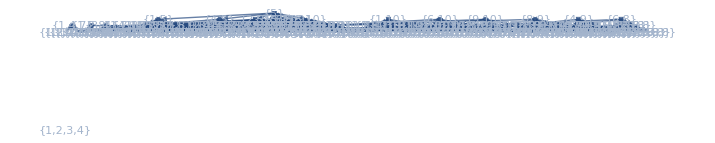

# codimension | 0 | 1 | 2 | 3 | 4
# boundaries | 0 | 1 | 15 | 72 | 125

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

```mathematica
basis=bdyBasis[[2]]//Flatten
```

{⟨5,11,12,13⟩,⟨1,5,12,13⟩,⟨1,10,12,13⟩,⟨2,5,11,13⟩,⟨3,5,11,12⟩,⟨4,5,11,12⟩,⟨4,9,11,12⟩,⟨5,6,11,13⟩,⟨5,7,11,12⟩,⟨5,8,11,13⟩,⟨5,9,11,12⟩,⟨5,10,12,13⟩,⟨6,8,11,13⟩,⟨6,10,11,13⟩,⟨6,10,12,13⟩,⟨8,9,11,12⟩,⟨8,9,11,13⟩,⟨9,10,11,12⟩,⟨9,10,12,13⟩,⟨1,2,5,13⟩,⟨1,2,8,13⟩,⟨1,2,10,13⟩,⟨1,3,5,12⟩,⟨1,3,10,12⟩,⟨1,4,5,12⟩,⟨1,4,7,12⟩,⟨1,4,9,12⟩,⟨1,4,10,12⟩,⟨1,5,6,13⟩,⟨1,5,7,12⟩,⟨1,5,8,13⟩,⟨1,5,9,12⟩,⟨1,6,8,13⟩,⟨1,6,10,13⟩,⟨1,7,8,12⟩,⟨1,7,8,13⟩,⟨1,7,10,12⟩,⟨1,8,9,12⟩,⟨1,8,9,13⟩,⟨1,8,10,13⟩,⟨1,9,10,12⟩,⟨2,3,5,11⟩,⟨2,4,5,11⟩,⟨2,4,9,11⟩,⟨2,5,6,13⟩,⟨2,5,7,11⟩,⟨2,5,8,13⟩,⟨2,5,9,11⟩,⟨2,5,10,13⟩,⟨2,6,8,13⟩,⟨2,6,10,13⟩,⟨2,8,9,11⟩,⟨2,8,9,13⟩,⟨2,9,10,11⟩,⟨2,9,10,13⟩,⟨3,4,5,11⟩,⟨3,4,6,11⟩,⟨3,4,9,11⟩,⟨3,5,6,11⟩,⟨3,5,7,11⟩,⟨3,5,8,11⟩,⟨3,5,9,11⟩,⟨3,5,10,12⟩,⟨3,6,8,11⟩,⟨3,6,10,11⟩,⟨3,6,10,12⟩,⟨3,8,9,11⟩,⟨3,9,10,11⟩,⟨3,9,10,12⟩,⟨4,5,6,11⟩,⟨4,5,7,12⟩,⟨4,5,8,11⟩,⟨4,5,10,12⟩,⟨4,6,7,11⟩,⟨4,6,7,12⟩,⟨4,6,8,11⟩,⟨4,6,9,11⟩,⟨4,6,10,11⟩,⟨4,6,10,12⟩,⟨4,7,9,12⟩,⟨4,8,9,11⟩,⟨4,9,10,12⟩,⟨5,6,7,11⟩,⟨5,6,7,12⟩,⟨5,6,7,13⟩,⟨5,6,9,11⟩,⟨5,6,10,13⟩,⟨5,7,8,11⟩,⟨5,7,8,12⟩,⟨5,7,8,13⟩,⟨5,7,9,12⟩,⟨5,7,10,12⟩,⟨5,8,9,11⟩,⟨5,8,10,13⟩,⟨5,9,10,12⟩,⟨6,7,8,11⟩,⟨6,7,8,12⟩,⟨6,7,8,13⟩,⟨6,7,10,11⟩,⟨6,7,10,12⟩,⟨6,8,9,11⟩,⟨6,8,10,13⟩,⟨6,9,10,11⟩,⟨6,9,10,12⟩,⟨7,8,9,12⟩,⟨7,8,9,13⟩,⟨7,9,10,12⟩,⟨8,9,10,11⟩,⟨8,9,10,13⟩,⟨1,2,3,4⟩,⟨1,2,3,5⟩,⟨1,2,3,8⟩,⟨1,2,3,10⟩,⟨1,2,4,5⟩,⟨1,2,4,7⟩,⟨1,2,4,8⟩,⟨1,2,4,9⟩,⟨1,2,4,10⟩,⟨1,2,5,7⟩,⟨1,2,5,9⟩,⟨1,2,7,8⟩,⟨1,2,7,10⟩,⟨1,2,8,9⟩,⟨1,2,9,10⟩,⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,9⟩,⟨1,3,4,10⟩,⟨1,3,5,6⟩,⟨1,3,5,7⟩,⟨1,3,5,8⟩,⟨1,3,5,9⟩,⟨1,3,6,8⟩,⟨1,3,6,10⟩,⟨1,3,7,8⟩,⟨1,3,7,10⟩,⟨1,3,8,9⟩,⟨1,3,8,10⟩,⟨1,3,9,10⟩,⟨1,4,5,6⟩,⟨1,4,5,8⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,6,10⟩,⟨1,4,7,8⟩,⟨1,4,8,9⟩,⟨1,4,8,10⟩,⟨1,5,6,7⟩,⟨1,5,6,9⟩,⟨1,5,7,8⟩,⟨1,5,8,9⟩,⟨1,6,7,8⟩,⟨1,6,7,10⟩,⟨1,6,8,9⟩,⟨1,6,9,10⟩,⟨1,7,8,10⟩,⟨1,8,9,10⟩,⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,9⟩,⟨2,3,5,6⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,5,10⟩,⟨2,3,6,8⟩,⟨2,3,6,10⟩,⟨2,3,8,9⟩,⟨2,3,9,10⟩,⟨2,4,5,6⟩,⟨2,4,5,7⟩,⟨2,4,5,8⟩,⟨2,4,5,10⟩,⟨2,4,6,7⟩,⟨2,4,6,8⟩,⟨2,4,6,9⟩,⟨2,4,6,10⟩,⟨2,4,7,9⟩,⟨2,4,8,9⟩,⟨2,4,9,10⟩,⟨2,5,6,7⟩,⟨2,5,6,9⟩,⟨2,5,7,8⟩,⟨2,5,7,9⟩,⟨2,5,7,10⟩,⟨2,5,8,9⟩,⟨2,5,9,10⟩,⟨2,6,7,8⟩,⟨2,6,7,10⟩,⟨2,6,8,9⟩,⟨2,6,9,10⟩,⟨2,7,8,9⟩,⟨2,7,9,10⟩,⟨3,4,5,7⟩,⟨3,4,5,10⟩,⟨3,4,6,7⟩,⟨3,4,6,10⟩,⟨3,4,7,9⟩,⟨3,4,9,10⟩,⟨3,5,6,7⟩,⟨3,5,6,10⟩,⟨3,5,7,8⟩,⟨3,5,7,9⟩,⟨3,5,7,10⟩,⟨3,5,8,10⟩,⟨3,5,9,10⟩,⟨3,6,7,8⟩,⟨3,6,7,10⟩,⟨3,6,8,10⟩,⟨3,7,8,9⟩,⟨3,7,9,10⟩,⟨3,8,9,10⟩,⟨4,5,6,7⟩,⟨4,5,6,10⟩,⟨4,5,7,8⟩,⟨4,5,8,10⟩,⟨4,6,7,8⟩,⟨4,6,7,9⟩,⟨4,6,8,10⟩,⟨4,6,9,10⟩,⟨4,7,8,9⟩,⟨4,8,9,10⟩,⟨5,6,7,9⟩,⟨5,6,7,10⟩,⟨5,6,9,10⟩,⟨5,7,8,9⟩,⟨5,7,8,10⟩,⟨5,8,9,10⟩,⟨6,7,8,9⟩,⟨6,7,8,10⟩,⟨6,7,9,10⟩,⟨6,8,9,10⟩,⟨7,8,9,10⟩}

```mathematica
basis//Length
```

234

```mathematica
EchoTiming[A = AMatrix[]];
A[[1]] // MatrixPlot
```

$Aborted

Part::partd: Part specification A⟦1⟧ is longer than depth of object.

A⟦1⟧

### Basis reduction: filtering

The stored A-matrix from previous overcomplete set of basis functions:

```mathematica
ClearAll[basis,A0,A];
Get[FileNameJoin[{NotebookDirectory[],"storage","basis_four-site-chain"}]];
Get[FileNameJoin[{NotebookDirectory[],"storage","A_four-site-chain"}]];
Get[FileNameJoin[{NotebookDirectory[],"storage","A0_four-site-chain"}]];
```

```mathematica
basis//Length
A0[[1]]//Length
A[[1]]//Length
```

234

234

221

```mathematica
EchoTiming[Amatrix=ATotal[A0]];
%//MatrixPlot
```

7.71104

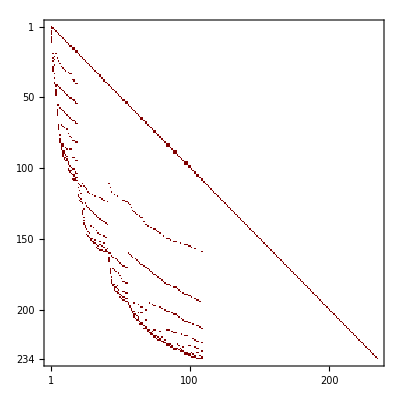

```mathematica
Amatrix//Letter
%//Length
```

{X1+X2+X3+X4,X1-Y12,X2+X3+X4-Y12,X1+Y12,X2+X3+X4+Y12,X1-Y12-2 Y23,X1+X2-Y23,X3+X4-Y23,X3+X4-2 Y12-Y23,X2-Y12-Y23,X1+X3+X4-Y12-Y23,-((X1+Y12) (-X2+Y12-Y23)),X2+Y12-Y23,-((X1+Y12) (X2+Y12-Y23)),X3+X4+2 Y12-Y23,X1+X2+Y23,X3+X4+Y23,(X2+Y12-Y23) (X3+X4+Y23),X2-Y12+Y23,X1-X3-X4-Y12+Y23,-((X1+Y12) (-X2+Y12+Y23)),X2+Y12+Y23,-((X1+Y12) (X2+Y12+Y23)),(X1-Y12-2 Y23) (X2+Y12+Y23),(X3+X4-Y23) (X2+Y12+Y23),(X3+X4+Y23) (X2+Y12+Y23),X1-Y12+2 Y23,(X2+Y12-Y23) (X1-Y12+2 Y23),X1-Y12-2 Y34,X1-Y12-2 Y23-2 Y34,X1+X2-Y23-2 Y34,X2-Y12-Y23-2 Y34,X2+Y12-Y23-2 Y34,X2+Y12+Y23-2 Y34,X1-Y12+2 Y23-2 Y34,X1+X2+X3-Y34,X4-Y34,X4-2 Y12-Y34,X2+X3-Y12-Y34,X1+X4-Y12-Y34,X2+X3+Y12-Y34,X4+2 Y12-Y34,X4-2 Y23-Y34,X4-2 Y12-2 Y23-Y34,X1+X4-Y12-2 Y23-Y34,X4+2 Y12-2 Y23-Y34,X3-Y23-Y34,X1+X2+X4-Y23-Y34,X3-2 Y12-Y23-Y34,X1-X3-Y12-Y23-Y34,X1+X3-Y12-Y23-Y34,X2+X4-Y12-Y23-Y34,X2+X4+Y12-Y23-Y34,X3+2 Y12-Y23-Y34,X3+Y23-Y34,X1-X3-Y12+Y23-Y34,X2+X4+Y12+Y23-Y34,X4+2 Y23-Y34,X4-2 Y12+2 Y23-Y34,X1+X4-Y12+2 Y23-Y34,X4+2 Y12+2 Y23-Y34,X1+X2+X3+Y34,X4+Y34,X2+X3-Y12+Y34,X1-X4-Y12+Y34,X2+X3+Y12+Y34,X1-X4-Y12-2 Y23+Y34,X3-Y23+Y34,X1+X2-X4-Y23+Y34,X3-2 Y12-Y23+Y34,X1+X3-Y12-Y23+Y34,X2-X4-Y12-Y23+Y34,X2-X4+Y12-Y23+Y34,X3+2 Y12-Y23+Y34,X3+Y23+Y34,X3-2 Y12+Y23+Y34,X1-X3-Y12+Y23+Y34,X1+X3-Y12+Y23+Y34,X2-X4+Y12+Y23+Y34,X3+2 Y12+Y23+Y34,X1-X4-Y12+2 Y23+Y34,X1-Y12+2 Y34,X1-Y12-2 Y23+2 Y34,X1+X2-Y23+2 Y34,X2-Y12-Y23+2 Y34,X2+Y12-Y23+2 Y34,X2+Y12+Y23+2 Y34,X1-Y12+2 Y23+2 Y34}

88

#### level 0

```mathematica
dRep=Thread[(d/@basis)->Coefficient[Amatrix,e].basis];
```

```mathematica
l0={Log[X1+Y12],Log[X2+Y12+Y23],Log[X3+Y23+Y34],Log[X4+Y34]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y12],Log[X2-Y12-Y23],Log[X2+Y12-Y23],Log[X2-Y12+Y23],Log[X4-Y34],Log[X3-Y23-Y34],Log[X3+Y23-Y34],Log[X3-Y23+Y34]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
Basis=Join[Basis,lv2];
```

{-⟨2,3,4,6⟩-⟨2,3,6,8⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,8⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨3,4,6,11⟩+⟨3,4,7,9⟩+⟨3,4,9,11⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨3,6,8,11⟩+⟨4,5,6,11⟩+⟨4,5,8,10⟩-⟨4,5,8,11⟩+⟨4,6,8,11⟩+⟨4,6,9,11⟩-⟨5,6,9,11⟩,-⟨1,3,4,9⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,4,5,8⟩-⟨1,4,5,12⟩+⟨1,4,9,12⟩-⟨1,5,9,12⟩+⟨3,4,9,11⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨4,5,8,11⟩,⟨1,3,4,7⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩-⟨1,4,7,12⟩+⟨1,4,8,10⟩+⟨1,4,10,12⟩-⟨1,7,10,12⟩+⟨3,4,7,9⟩-⟨3,4,9,11⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩-⟨3,5,8,11⟩+⟨3,5,9,11⟩+⟨4,5,8,10⟩+⟨4,5,8,11⟩+⟨4,5,10,12⟩+⟨4,7,9,12⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩,⟨1,3,4,6⟩+⟨1,3,6,8⟩-⟨1,4,5,6⟩+⟨1,4,5,12⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩-⟨1,4,9,12⟩+⟨1,5,6,9⟩+⟨1,5,9,12⟩-⟨3,4,6,11⟩-⟨3,6,8,11⟩+⟨4,5,6,11⟩+⟨4,6,8,11⟩+⟨4,6,9,11⟩-⟨5,6,9,11⟩,⟨1,2,3,8⟩-⟨1,2,7,10⟩-⟨1,2,8,13⟩+⟨1,2,10,13⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,3,6,8⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩+⟨1,5,6,9⟩+⟨1,5,6,13⟩-⟨1,5,8,13⟩+⟨1,6,8,13⟩-⟨1,8,10,13⟩-⟨2,3,6,8⟩-⟨2,5,6,9⟩-⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,5,10,13⟩-⟨2,6,8,13⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨5,8,10,13⟩,⟨1,2,4,10⟩+⟨1,2,10,13⟩-⟨1,4,5,6⟩-⟨1,4,5,12⟩+⟨1,4,10,12⟩+⟨1,5,6,13⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩-⟨2,5,6,13⟩+⟨2,5,10,13⟩+⟨4,5,10,12⟩,-⟨1,2,4,8⟩-⟨1,2,8,13⟩+⟨1,4,5,8⟩+⟨1,4,5,12⟩-⟨1,4,6,8⟩+⟨1,4,8,10⟩-⟨1,4,10,12⟩-⟨1,5,8,13⟩+⟨1,6,8,13⟩-⟨1,8,10,13⟩+⟨2,4,6,8⟩-⟨2,6,8,13⟩+⟨4,5,8,10⟩-⟨4,5,10,12⟩+⟨5,8,10,13⟩,-⟨1,2,4,7⟩-⟨1,2,7,10⟩-⟨1,2,10,13⟩-⟨1,4,6,9⟩-⟨1,4,7,12⟩+⟨1,4,9,12⟩+⟨1,5,6,9⟩-⟨1,5,6,13⟩-⟨1,5,9,12⟩-⟨1,7,10,12⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,13⟩+⟨4,7,9,12⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩}

8

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basis;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten;
Do[If[CheckDependent[lv2Old,i,Basis],,Join[Basis,lv2Old[[i]]]],{i,1,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

9

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,8}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2-Y23],Log[X3+X4-Y23],Log[X1+X2+Y23],Log[X3+X4+Y23],Log[X2+X3-Y12-Y34],Log[X2+X3+Y12-Y34],Log[X2+X3-Y12+Y34],Log[X2+X3+Y12+Y34]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
-2 ⟨1,4,5,12⟩+⟨1,5,12,13⟩-⟨4,5,11,12⟩ | 2 ⟨1,4,5,12⟩-⟨1,5,12,13⟩+⟨4,5,11,12⟩
2 ⟨1,4,9,12⟩-2 ⟨1,5,9,12⟩-⟨1,5,12,13⟩+⟨4,9,11,12⟩-⟨5,9,11,12⟩ | -2 ⟨1,4,9,12⟩+2 ⟨1,5,9,12⟩+⟨1,5,12,13⟩-⟨4,9,11,12⟩+⟨5,9,11,12⟩
2 ⟨3,4,9,11⟩+2 ⟨3,5,8,11⟩-2 ⟨3,5,9,11⟩-2 ⟨4,5,8,11⟩-⟨4,5,11,12⟩+⟨4,9,11,12⟩-⟨5,9,11,12⟩ | -2 ⟨3,4,9,11⟩-2 ⟨3,5,8,11⟩+2 ⟨3,5,9,11⟩+2 ⟨4,5,8,11⟩+⟨4,5,11,12⟩-⟨4,9,11,12⟩+⟨5,9,11,12⟩
2 ⟨3,4,6,11⟩+2 ⟨3,6,8,11⟩-2 ⟨4,5,6,11⟩-⟨4,5,11,12⟩-2 ⟨4,6,8,11⟩-2 ⟨4,6,9,11⟩+⟨4,9,11,12⟩+2 ⟨5,6,9,11⟩-⟨5,9,11,12⟩ | -2 ⟨3,4,6,11⟩-2 ⟨3,6,8,11⟩+2 ⟨4,5,6,11⟩+⟨4,5,11,12⟩+2 ⟨4,6,8,11⟩+2 ⟨4,6,9,11⟩-⟨4,9,11,12⟩-2 ⟨5,6,9,11⟩+⟨5,9,11,12⟩
-2 ⟨1,2,10,13⟩-2 ⟨1,5,6,13⟩-⟨1,5,12,13⟩+⟨1,10,12,13⟩+2 ⟨2,5,6,13⟩-2 ⟨2,5,10,13⟩-⟨5,10,12,13⟩ | 2 ⟨1,2,10,13⟩+2 ⟨1,5,6,13⟩+⟨1,5,12,13⟩-⟨1,10,12,13⟩-2 ⟨2,5,6,13⟩+2 ⟨2,5,10,13⟩+⟨5,10,12,13⟩
-2 ⟨1,4,10,12⟩+⟨1,10,12,13⟩-2 ⟨4,5,10,12⟩-⟨4,5,11,12⟩-⟨5,10,12,13⟩ | 2 ⟨1,4,10,12⟩-⟨1,10,12,13⟩+2 ⟨4,5,10,12⟩+⟨4,5,11,12⟩+⟨5,10,12,13⟩
-2 ⟨1,2,8,13⟩-2 ⟨1,5,8,13⟩-⟨1,5,12,13⟩+2 ⟨1,6,8,13⟩-2 ⟨1,8,10,13⟩+⟨1,10,12,13⟩-2 ⟨2,6,8,13⟩+2 ⟨5,8,10,13⟩-⟨5,10,12,13⟩ | 2 ⟨1,2,8,13⟩+2 ⟨1,5,8,13⟩+⟨1,5,12,13⟩-2 ⟨1,6,8,13⟩+2 ⟨1,8,10,13⟩-⟨1,10,12,13⟩+2 ⟨2,6,8,13⟩-2 ⟨5,8,10,13⟩+⟨5,10,12,13⟩
-2 ⟨1,4,7,12⟩-2 ⟨1,7,10,12⟩+⟨1,10,12,13⟩+2 ⟨4,7,9,12⟩-⟨4,9,11,12⟩-2 ⟨5,7,9,12⟩+2 ⟨5,7,10,12⟩+⟨5,9,11,12⟩-⟨5,10,12,13⟩ | 2 ⟨1,4,7,12⟩+2 ⟨1,7,10,12⟩-⟨1,10,12,13⟩-2 ⟨4,7,9,12⟩+⟨4,9,11,12⟩+2 ⟨5,7,9,12⟩-2 ⟨5,7,10,12⟩-⟨5,9,11,12⟩+⟨5,10,12,13⟩)

{-2 ⟨1,4,5,12⟩+⟨1,5,12,13⟩-⟨4,5,11,12⟩,2 ⟨1,4,9,12⟩-2 ⟨1,5,9,12⟩-⟨1,5,12,13⟩+⟨4,9,11,12⟩-⟨5,9,11,12⟩,2 ⟨3,4,9,11⟩+2 ⟨3,5,8,11⟩-2 ⟨3,5,9,11⟩-2 ⟨4,5,8,11⟩-⟨4,5,11,12⟩+⟨4,9,11,12⟩-⟨5,9,11,12⟩,2 ⟨3,4,6,11⟩+2 ⟨3,6,8,11⟩-2 ⟨4,5,6,11⟩-⟨4,5,11,12⟩-2 ⟨4,6,8,11⟩-2 ⟨4,6,9,11⟩+⟨4,9,11,12⟩+2 ⟨5,6,9,11⟩-⟨5,9,11,12⟩,-2 ⟨1,2,10,13⟩-2 ⟨1,5,6,13⟩-⟨1,5,12,13⟩+⟨1,10,12,13⟩+2 ⟨2,5,6,13⟩-2 ⟨2,5,10,13⟩-⟨5,10,12,13⟩,-2 ⟨1,4,10,12⟩+⟨1,10,12,13⟩-2 ⟨4,5,10,12⟩-⟨4,5,11,12⟩-⟨5,10,12,13⟩,-2 ⟨1,2,8,13⟩-2 ⟨1,5,8,13⟩-⟨1,5,12,13⟩+2 ⟨1,6,8,13⟩-2 ⟨1,8,10,13⟩+⟨1,10,12,13⟩-2 ⟨2,6,8,13⟩+2 ⟨5,8,10,13⟩-⟨5,10,12,13⟩,-2 ⟨1,4,7,12⟩-2 ⟨1,7,10,12⟩+⟨1,10,12,13⟩+2 ⟨4,7,9,12⟩-⟨4,9,11,12⟩-2 ⟨5,7,9,12⟩+2 ⟨5,7,10,12⟩+⟨5,9,11,12⟩-⟨5,10,12,13⟩}

```mathematica
Basis=Join[Basis,lv3];
Basis//Length
```

17

```mathematica
lv3Old=Coefficient[d2,#]&/@l1//Flatten;
EchoTiming[Do[If[CheckDependent[lv3Old,i,Basis],,Basis=Append[Basis,lv3Old[[i]]]],{i,1,Length[lv3Old]}]]
Basis//Length
```

5.24253

31

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,8,22}

#### level 3

```mathematica
d3=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l3=Cases[%,_Log,Infinity]//Union;
Complement[l3,l2]
```

{Log[X2+X3+X4-Y12],Log[X2+X3+X4+Y12],Log[X1+X2+X3-Y34],Log[X1+X2+X3+Y34]}

```mathematica
Coefficient[d3,#]&/@Complement[l3,l2];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 11x1 to 3*)
lv4=%[[All;;,1]] //DeleteCases[0]
```

{3 ⟨1,5,12,13⟩-⟨5,11,12,13⟩,-3 ⟨4,5,11,12⟩-⟨5,11,12,13⟩,-3 ⟨4,9,11,12⟩+3 ⟨5,9,11,12⟩-⟨5,11,12,13⟩,3 ⟨1,10,12,13⟩-3 ⟨5,10,12,13⟩-⟨5,11,12,13⟩}

```mathematica
Basis=Join[Basis,lv4];
Basis//Length
```

35

```mathematica
lv4Old=Coefficient[d3,#]&/@(Complement[l3,Complement[l3,l2]])//Flatten;
EchoTiming[Do[If[CheckDependent[lv4Old,i,Basis],,Basis=Append[Basis,lv4Old[[i]]]],{i,1,Length[lv4Old]}]]
Basis//Length
```

37.6233

55

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,8,22,24}

#### level 4

```mathematica
d4=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l4=Cases[%,_Log,Infinity]//Union;
Complement[l4,l3]
```

{Log[X1+X2+X3+X4]}

```mathematica
Coefficient[d4,#]&/@Complement[l4,l3];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 11x1 to 3*)
lv5=%[[All;;,1]] //DeleteCases[0]
```

{-4 ⟨5,11,12,13⟩}

```mathematica
Basis=Join[Basis,lv5];
Basis//Length
```

56

```mathematica
lv5Old=Coefficient[d4,#]&/@(Complement[l4,Complement[l4,l3]])//Flatten;
EchoTiming[Do[If[CheckDependent[lv5Old,i,Basis],,Basis=Append[Basis,lv5Old[[i]]]],{i,1,Length[lv5Old]}]]
Basis//Length
```

59.7091

64

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,8,22,24,9}

#### close at level 4:

```mathematica
letters={l0,l1,l2,l3,l4}//Flatten//Union
%//Length
```

{Log[X1+X2+X3+X4],Log[X1-Y12],Log[X2+X3+X4-Y12],Log[X1+Y12],Log[X2+X3+X4+Y12],Log[X1+X2-Y23],Log[X3+X4-Y23],Log[X2-Y12-Y23],Log[X2+Y12-Y23],Log[X1+X2+Y23],Log[X3+X4+Y23],Log[X2-Y12+Y23],Log[X2+Y12+Y23],Log[X1+X2+X3-Y34],Log[X4-Y34],Log[X2+X3-Y12-Y34],Log[X2+X3+Y12-Y34],Log[X3-Y23-Y34],Log[X3+Y23-Y34],Log[X1+X2+X3+Y34],Log[X4+Y34],Log[X2+X3-Y12+Y34],Log[X2+X3+Y12+Y34],Log[X3-Y23+Y34],Log[X3+Y23+Y34]}

25

```mathematica
d5=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l5=Cases[%,_Log,Infinity]//Union
Complement[l5,letters]
```

{Log[X1+X2+X3+X4],Log[X1-Y12],Log[X2+X3+X4-Y12],Log[X1+Y12],Log[X2+X3+X4+Y12],Log[X1+X2-Y23],Log[X3+X4-Y23],Log[X2-Y12-Y23],Log[X2+Y12-Y23],Log[X1+X2+Y23],Log[X3+X4+Y23],Log[X2-Y12+Y23],Log[X2+Y12+Y23],Log[X4-Y34],Log[X1+X2+X3+Y34],Log[X2+X3-Y12+Y34],Log[X2+X3+Y12+Y34],Log[X3-Y23+Y34]}

{}

so there is no new letters appearing.

```mathematica
lv6Old=Coefficient[d5,#]&/@letters//Flatten;
EchoTiming[Do[If[CheckDependent[lv6Old,i,Basis],,Basis=Append[Basis,lv6Old[[i]]]],{i,1,Length[lv6Old]}]]
Basis//Length
```

23.1289

64

since there is no new basis introduced, we show that the differentiation closes at level 4.

#### summary: all physical basis

64 = 1 + (7+1) + (8+14) + (4+20) + (1+8)
25 = 4 + 8 + 8 + 4 + 1

```mathematica
Basis//MatrixForm
Basis//Length
```

(-⟨1,2,3,4⟩+⟨1,2,3,8⟩-⟨1,2,4,7⟩-⟨1,2,4,8⟩+⟨1,2,4,10⟩-⟨1,2,7,10⟩+⟨1,3,4,6⟩+⟨1,3,4,7⟩-⟨1,3,4,9⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,3,6,8⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩-⟨1,4,5,6⟩+⟨1,4,5,8⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩+⟨1,4,8,10⟩+⟨1,5,6,9⟩-⟨2,3,4,6⟩-⟨2,3,6,8⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,8⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨3,4,7,9⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨4,5,8,10⟩
-⟨2,3,4,6⟩-⟨2,3,6,8⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,8⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨3,4,6,11⟩+⟨3,4,7,9⟩+⟨3,4,9,11⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨3,6,8,11⟩+⟨4,5,6,11⟩+⟨4,5,8,10⟩-⟨4,5,8,11⟩+⟨4,6,8,11⟩+⟨4,6,9,11⟩-⟨5,6,9,11⟩
-⟨1,3,4,9⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,4,5,8⟩-⟨1,4,5,12⟩+⟨1,4,9,12⟩-⟨1,5,9,12⟩+⟨3,4,9,11⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨4,5,8,11⟩
⟨1,3,4,7⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩-⟨1,4,7,12⟩+⟨1,4,8,10⟩+⟨1,4,10,12⟩-⟨1,7,10,12⟩+⟨3,4,7,9⟩-⟨3,4,9,11⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩-⟨3,5,8,11⟩+⟨3,5,9,11⟩+⟨4,5,8,10⟩+⟨4,5,8,11⟩+⟨4,5,10,12⟩+⟨4,7,9,12⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩
⟨1,3,4,6⟩+⟨1,3,6,8⟩-⟨1,4,5,6⟩+⟨1,4,5,12⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩-⟨1,4,9,12⟩+⟨1,5,6,9⟩+⟨1,5,9,12⟩-⟨3,4,6,11⟩-⟨3,6,8,11⟩+⟨4,5,6,11⟩+⟨4,6,8,11⟩+⟨4,6,9,11⟩-⟨5,6,9,11⟩
⟨1,2,3,8⟩-⟨1,2,7,10⟩-⟨1,2,8,13⟩+⟨1,2,10,13⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,3,6,8⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩+⟨1,5,6,9⟩+⟨1,5,6,13⟩-⟨1,5,8,13⟩+⟨1,6,8,13⟩-⟨1,8,10,13⟩-⟨2,3,6,8⟩-⟨2,5,6,9⟩-⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,5,10,13⟩-⟨2,6,8,13⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨5,8,10,13⟩
⟨1,2,4,10⟩+⟨1,2,10,13⟩-⟨1,4,5,6⟩-⟨1,4,5,12⟩+⟨1,4,10,12⟩+⟨1,5,6,13⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩-⟨2,5,6,13⟩+⟨2,5,10,13⟩+⟨4,5,10,12⟩
-⟨1,2,4,8⟩-⟨1,2,8,13⟩+⟨1,4,5,8⟩+⟨1,4,5,12⟩-⟨1,4,6,8⟩+⟨1,4,8,10⟩-⟨1,4,10,12⟩-⟨1,5,8,13⟩+⟨1,6,8,13⟩-⟨1,8,10,13⟩+⟨2,4,6,8⟩-⟨2,6,8,13⟩+⟨4,5,8,10⟩-⟨4,5,10,12⟩+⟨5,8,10,13⟩
-⟨1,2,4,7⟩-⟨1,2,7,10⟩-⟨1,2,10,13⟩-⟨1,4,6,9⟩-⟨1,4,7,12⟩+⟨1,4,9,12⟩+⟨1,5,6,9⟩-⟨1,5,6,13⟩-⟨1,5,9,12⟩-⟨1,7,10,12⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,13⟩+⟨4,7,9,12⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩
-2 ⟨1,4,5,12⟩+⟨1,5,12,13⟩-⟨4,5,11,12⟩
2 ⟨1,4,9,12⟩-2 ⟨1,5,9,12⟩-⟨1,5,12,13⟩+⟨4,9,11,12⟩-⟨5,9,11,12⟩
2 ⟨3,4,9,11⟩+2 ⟨3,5,8,11⟩-2 ⟨3,5,9,11⟩-2 ⟨4,5,8,11⟩-⟨4,5,11,12⟩+⟨4,9,11,12⟩-⟨5,9,11,12⟩
2 ⟨3,4,6,11⟩+2 ⟨3,6,8,11⟩-2 ⟨4,5,6,11⟩-⟨4,5,11,12⟩-2 ⟨4,6,8,11⟩-2 ⟨4,6,9,11⟩+⟨4,9,11,12⟩+2 ⟨5,6,9,11⟩-⟨5,9,11,12⟩
-2 ⟨1,2,10,13⟩-2 ⟨1,5,6,13⟩-⟨1,5,12,13⟩+⟨1,10,12,13⟩+2 ⟨2,5,6,13⟩-2 ⟨2,5,10,13⟩-⟨5,10,12,13⟩
-2 ⟨1,4,10,12⟩+⟨1,10,12,13⟩-2 ⟨4,5,10,12⟩-⟨4,5,11,12⟩-⟨5,10,12,13⟩
-2 ⟨1,2,8,13⟩-2 ⟨1,5,8,13⟩-⟨1,5,12,13⟩+2 ⟨1,6,8,13⟩-2 ⟨1,8,10,13⟩+⟨1,10,12,13⟩-2 ⟨2,6,8,13⟩+2 ⟨5,8,10,13⟩-⟨5,10,12,13⟩
-2 ⟨1,4,7,12⟩-2 ⟨1,7,10,12⟩+⟨1,10,12,13⟩+2 ⟨4,7,9,12⟩-⟨4,9,11,12⟩-2 ⟨5,7,9,12⟩+2 ⟨5,7,10,12⟩+⟨5,9,11,12⟩-⟨5,10,12,13⟩
⟨3,4,7,9⟩+⟨3,4,9,11⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩+⟨4,5,8,10⟩-⟨4,5,8,11⟩+⟨4,5,10,12⟩-⟨4,5,11,12⟩+⟨4,7,9,12⟩+⟨4,9,11,12⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩-⟨5,9,11,12⟩
-⟨2,3,6,8⟩-⟨2,5,6,9⟩-⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,5,10,13⟩-⟨2,6,8,13⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨3,6,8,11⟩-⟨5,6,9,11⟩+⟨5,6,11,13⟩+⟨5,8,10,13⟩-⟨5,8,11,13⟩+⟨6,8,11,13⟩
⟨2,4,5,6⟩-⟨2,4,5,10⟩-⟨2,5,6,13⟩+⟨2,5,10,13⟩+⟨4,5,6,11⟩+⟨4,5,10,12⟩-⟨4,5,11,12⟩+⟨5,6,11,13⟩
⟨2,4,6,8⟩-⟨2,6,8,13⟩+⟨4,5,8,10⟩-⟨4,5,8,11⟩-⟨4,5,10,12⟩+⟨4,5,11,12⟩+⟨4,6,8,11⟩+⟨5,8,10,13⟩-⟨5,8,11,13⟩+⟨6,8,11,13⟩
⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,13⟩+⟨4,6,9,11⟩+⟨4,7,9,12⟩+⟨4,9,11,12⟩-⟨5,6,9,11⟩-⟨5,6,11,13⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩-⟨5,9,11,12⟩
-⟨1,3,5,8⟩+⟨1,3,5,9⟩-⟨1,5,8,13⟩-⟨1,5,9,12⟩+⟨1,5,12,13⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨5,8,11,13⟩
⟨1,4,5,8⟩-⟨1,4,5,12⟩-⟨1,5,8,13⟩+⟨1,5,12,13⟩-⟨4,5,8,11⟩-⟨5,8,11,13⟩
⟨1,3,7,10⟩-⟨1,3,8,10⟩-⟨1,7,10,12⟩-⟨1,8,10,13⟩-⟨1,10,12,13⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩-⟨3,5,8,11⟩+⟨3,5,9,11⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩+⟨5,8,10,13⟩+⟨5,8,11,13⟩+⟨5,10,12,13⟩
⟨1,4,8,10⟩+⟨1,4,10,12⟩-⟨1,8,10,13⟩-⟨1,10,12,13⟩+⟨4,5,8,10⟩+⟨4,5,8,11⟩+⟨4,5,10,12⟩+⟨5,8,10,13⟩+⟨5,8,11,13⟩+⟨5,10,12,13⟩
⟨1,3,6,8⟩+⟨1,5,6,9⟩+⟨1,5,6,13⟩+⟨1,5,9,12⟩-⟨1,5,12,13⟩+⟨1,6,8,13⟩-⟨3,6,8,11⟩-⟨5,6,9,11⟩+⟨5,6,11,13⟩+⟨6,8,11,13⟩
-⟨1,4,5,6⟩+⟨1,4,5,12⟩+⟨1,5,6,13⟩-⟨1,5,12,13⟩+⟨4,5,6,11⟩+⟨5,6,11,13⟩
-⟨1,4,6,8⟩+⟨1,6,8,13⟩+⟨4,6,8,11⟩+⟨6,8,11,13⟩
-⟨1,4,6,9⟩-⟨1,4,9,12⟩+⟨1,5,6,9⟩-⟨1,5,6,13⟩+⟨1,5,9,12⟩+⟨1,5,12,13⟩+⟨4,6,9,11⟩-⟨5,6,9,11⟩-⟨5,6,11,13⟩
-⟨1,2,7,10⟩+⟨1,2,10,13⟩+⟨1,5,6,9⟩+⟨1,5,6,13⟩-⟨1,5,9,12⟩+⟨1,5,12,13⟩-⟨1,7,10,12⟩-⟨1,10,12,13⟩-⟨2,5,6,9⟩-⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,5,10,13⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩+⟨5,10,12,13⟩
3 ⟨1,5,12,13⟩-⟨5,11,12,13⟩
-3 ⟨4,5,11,12⟩-⟨5,11,12,13⟩
-3 ⟨4,9,11,12⟩+3 ⟨5,9,11,12⟩-⟨5,11,12,13⟩
3 ⟨1,10,12,13⟩-3 ⟨5,10,12,13⟩-⟨5,11,12,13⟩
2 ⟨2,5,6,13⟩-2 ⟨2,5,10,13⟩-2 ⟨5,6,11,13⟩-⟨5,10,12,13⟩+⟨5,11,12,13⟩
-2 ⟨4,5,10,12⟩+2 ⟨4,5,11,12⟩-⟨5,10,12,13⟩+⟨5,11,12,13⟩
-2 ⟨2,6,8,13⟩+2 ⟨5,8,10,13⟩-2 ⟨5,8,11,13⟩-⟨5,10,12,13⟩+⟨5,11,12,13⟩+2 ⟨6,8,11,13⟩
2 ⟨4,7,9,12⟩+2 ⟨4,9,11,12⟩-2 ⟨5,7,9,12⟩+2 ⟨5,7,10,12⟩-2 ⟨5,9,11,12⟩-⟨5,10,12,13⟩+⟨5,11,12,13⟩
-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩+⟨5,8,10,13⟩-⟨5,8,11,13⟩-⟨5,9,11,12⟩+⟨5,10,12,13⟩-⟨5,11,12,13⟩
⟨4,5,8,10⟩-⟨4,5,8,11⟩+⟨4,5,10,12⟩-⟨4,5,11,12⟩+⟨5,8,10,13⟩-⟨5,8,11,13⟩+⟨5,10,12,13⟩-⟨5,11,12,13⟩
-⟨2,5,6,9⟩-⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,5,10,13⟩-⟨5,6,9,11⟩+⟨5,6,11,13⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩-⟨5,9,11,12⟩+⟨5,10,12,13⟩-⟨5,11,12,13⟩
-⟨1,3,5,8⟩+⟨1,3,5,9⟩-⟨1,5,8,13⟩-⟨1,5,9,12⟩+⟨1,5,12,13⟩-⟨3,5,8,11⟩+⟨3,5,9,11⟩+⟨5,8,11,13⟩+⟨5,9,11,12⟩+⟨5,11,12,13⟩
⟨1,4,5,8⟩-⟨1,4,5,12⟩-⟨1,5,8,13⟩+⟨1,5,12,13⟩+⟨4,5,8,11⟩+⟨4,5,11,12⟩+⟨5,8,11,13⟩+⟨5,11,12,13⟩
⟨1,3,6,8⟩+⟨1,5,6,9⟩+⟨1,5,6,13⟩+⟨1,5,9,12⟩-⟨1,5,12,13⟩+⟨1,6,8,13⟩+⟨3,6,8,11⟩+⟨5,6,9,11⟩-⟨5,6,11,13⟩-⟨5,9,11,12⟩-⟨5,11,12,13⟩-⟨6,8,11,13⟩
-⟨1,4,5,6⟩+⟨1,4,5,12⟩+⟨1,5,6,13⟩-⟨1,5,12,13⟩-⟨4,5,6,11⟩-⟨4,5,11,12⟩-⟨5,6,11,13⟩-⟨5,11,12,13⟩
-⟨1,4,6,8⟩+⟨1,6,8,13⟩-⟨4,6,8,11⟩-⟨6,8,11,13⟩
-⟨1,4,6,9⟩-⟨1,4,9,12⟩+⟨1,5,6,9⟩-⟨1,5,6,13⟩+⟨1,5,9,12⟩+⟨1,5,12,13⟩-⟨4,6,9,11⟩+⟨4,9,11,12⟩+⟨5,6,9,11⟩+⟨5,6,11,13⟩-⟨5,9,11,12⟩+⟨5,11,12,13⟩
2 ⟨1,5,6,13⟩+⟨1,5,12,13⟩+2 ⟨5,6,11,13⟩-⟨5,11,12,13⟩
-2 ⟨1,5,8,13⟩+2 ⟨1,5,12,13⟩-2 ⟨5,8,11,13⟩
-2 ⟨1,8,10,13⟩-2 ⟨1,10,12,13⟩+2 ⟨5,8,10,13⟩+2 ⟨5,8,11,13⟩+2 ⟨5,10,12,13⟩
2 ⟨1,6,8,13⟩+2 ⟨6,8,11,13⟩
⟨1,5,6,9⟩+⟨1,5,6,13⟩+⟨1,5,9,12⟩-⟨1,5,12,13⟩-⟨5,6,9,11⟩+⟨5,6,11,13⟩
-⟨1,2,7,10⟩+⟨1,2,10,13⟩+⟨1,7,10,12⟩+⟨1,10,12,13⟩-⟨2,5,6,9⟩-⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,5,10,13⟩+⟨5,6,9,11⟩-⟨5,6,11,13⟩+⟨5,7,9,12⟩-⟨5,7,10,12⟩-⟨5,10,12,13⟩
-2 ⟨1,5,9,12⟩+2 ⟨1,5,12,13⟩-⟨5,9,11,12⟩-⟨5,11,12,13⟩
-4 ⟨5,11,12,13⟩
-3 ⟨5,10,12,13⟩+3 ⟨5,11,12,13⟩
2 ⟨5,8,10,13⟩-2 ⟨5,8,11,13⟩+2 ⟨5,10,12,13⟩-2 ⟨5,11,12,13⟩
-⟨2,5,6,9⟩-⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,5,10,13⟩-⟨5,6,9,11⟩+⟨5,6,11,13⟩+⟨5,7,9,12⟩-⟨5,7,10,12⟩+⟨5,9,11,12⟩-⟨5,10,12,13⟩+⟨5,11,12,13⟩
2 ⟨1,5,6,13⟩+⟨1,5,12,13⟩-2 ⟨5,6,11,13⟩+⟨5,11,12,13⟩
-2 ⟨1,5,8,13⟩+2 ⟨1,5,12,13⟩+2 ⟨5,8,11,13⟩+2 ⟨5,11,12,13⟩
2 ⟨1,6,8,13⟩-2 ⟨6,8,11,13⟩
⟨1,5,6,9⟩+⟨1,5,6,13⟩+⟨1,5,9,12⟩-⟨1,5,12,13⟩+⟨5,6,9,11⟩-⟨5,6,11,13⟩-⟨5,9,11,12⟩-⟨5,11,12,13⟩
-2 ⟨1,5,9,12⟩+2 ⟨1,5,12,13⟩+2 ⟨5,9,11,12⟩+2 ⟨5,11,12,13⟩)

64

see how this 64d subspace is embedded in the previous 234d space:

```mathematica
Basis/.Thread[basis->(Subscript[φ,#]&/@Range[basis//Length])]//MatrixForm
```

(-φ_110+φ_112-φ_115-φ_116+φ_118-φ_122+φ_126+φ_127-φ_128-φ_132+φ_133+φ_134+φ_137-φ_139-φ_141+φ_142-φ_144-φ_145+φ_149+φ_151-φ_161-φ_167+φ_171-φ_174+φ_176+φ_177-φ_179-φ_183+φ_185-φ_186+φ_199-φ_204+φ_205-φ_206+φ_217
-φ_57+φ_58+φ_61-φ_62-φ_64+φ_70-φ_72+φ_76+φ_77-φ_86-φ_161-φ_167+φ_171-φ_174+φ_176+φ_177-φ_179-φ_183+φ_185-φ_186+φ_199-φ_204+φ_205-φ_206+φ_217
-φ_25+φ_27-φ_32+φ_58+φ_61-φ_62-φ_72-φ_128-φ_132+φ_133+φ_142
-φ_26+φ_28-φ_37-φ_58-φ_61+φ_62+φ_72+φ_73+φ_80-φ_91+φ_92+φ_127+φ_137-φ_139+φ_149+φ_199-φ_204+φ_205-φ_206+φ_217
φ_25-φ_27+φ_32-φ_57-φ_64+φ_70+φ_76+φ_77-φ_86+φ_126+φ_134-φ_141-φ_144-φ_145+φ_151
-φ_21+φ_22+φ_29-φ_31+φ_33-φ_40-φ_45+φ_49-φ_50+φ_94+φ_112-φ_122-φ_132+φ_133+φ_134+φ_137-φ_139+φ_151-φ_167-φ_183+φ_185-φ_186-φ_204+φ_205-φ_206
φ_22-φ_25+φ_28+φ_29-φ_45+φ_49+φ_73+φ_118-φ_141+φ_171-φ_174
-φ_21+φ_25-φ_28-φ_31+φ_33-φ_40-φ_50-φ_73+φ_94-φ_116+φ_142-φ_144+φ_149+φ_176+φ_217
-φ_22-φ_26+φ_27-φ_29-φ_32-φ_37+φ_45-φ_49+φ_80-φ_91+φ_92-φ_115-φ_122-φ_145+φ_151+φ_177-φ_179-φ_183+φ_185-φ_186
φ_2-φ_6-2 φ_25
-φ_2+φ_7-φ_11+2 φ_27-2 φ_32
-φ_6+φ_7-φ_11+2 φ_58+2 φ_61-2 φ_62-2 φ_72
-φ_6+φ_7-φ_11+2 φ_57+2 φ_64-2 φ_70-2 φ_76-2 φ_77+2 φ_86
-φ_2+φ_3-φ_12-2 φ_22-2 φ_29+2 φ_45-2 φ_49
φ_3-φ_6-φ_12-2 φ_28-2 φ_73
-φ_2+φ_3-φ_12-2 φ_21-2 φ_31+2 φ_33-2 φ_40-2 φ_50+2 φ_94
φ_3-φ_7+φ_11-φ_12-2 φ_26-2 φ_37+2 φ_80-2 φ_91+2 φ_92
-φ_6+φ_7-φ_11+φ_58+φ_61-φ_62-φ_72+φ_73+φ_80-φ_91+φ_92+φ_199-φ_204+φ_205-φ_206+φ_217
φ_8-φ_10+φ_13-φ_45+φ_49-φ_50+φ_61-φ_62-φ_64-φ_86+φ_94-φ_167-φ_183+φ_185-φ_186-φ_204+φ_205-φ_206
-φ_6+φ_8-φ_45+φ_49+φ_70+φ_73+φ_171-φ_174
φ_6-φ_10+φ_13-φ_50-φ_72-φ_73+φ_76+φ_94+φ_176+φ_217
φ_7-φ_8-φ_11+φ_45-φ_49+φ_77+φ_80-φ_86-φ_91+φ_92+φ_177-φ_179-φ_183+φ_185-φ_186
φ_2-φ_10-φ_31-φ_32+φ_61-φ_62-φ_132+φ_133
φ_2-φ_10-φ_25-φ_31-φ_72+φ_142
-φ_3+φ_10+φ_12-φ_37-φ_40-φ_61+φ_62-φ_91+φ_92+φ_94+φ_137-φ_139-φ_204+φ_205-φ_206
-φ_3+φ_10+φ_12+φ_28-φ_40+φ_72+φ_73+φ_94+φ_149+φ_217
-φ_2+φ_8+φ_13+φ_29+φ_32+φ_33-φ_64-φ_86+φ_134+φ_151
-φ_2+φ_8+φ_25+φ_29+φ_70-φ_141
φ_13+φ_33+φ_76-φ_144
φ_2-φ_8-φ_27-φ_29+φ_32+φ_77-φ_86-φ_145+φ_151
φ_2-φ_3+φ_12+φ_22+φ_29-φ_32-φ_37-φ_45+φ_49-φ_91+φ_92-φ_122+φ_151-φ_183+φ_185-φ_186
-φ_1+3 φ_2
-φ_1-3 φ_6
-φ_1-3 φ_7+3 φ_11
-φ_1+3 φ_3-3 φ_12
φ_1-2 φ_8-φ_12+2 φ_45-2 φ_49
φ_1+2 φ_6-φ_12-2 φ_73
φ_1-2 φ_10-φ_12+2 φ_13-2 φ_50+2 φ_94
φ_1+2 φ_7-2 φ_11-φ_12+2 φ_80-2 φ_91+2 φ_92
-φ_1-φ_10-φ_11+φ_12+φ_61-φ_62-φ_91+φ_92+φ_94-φ_204+φ_205-φ_206
-φ_1-φ_6-φ_10+φ_12-φ_72+φ_73+φ_94+φ_217
-φ_1+φ_8-φ_11+φ_12-φ_45+φ_49-φ_86-φ_91+φ_92-φ_183+φ_185-φ_186
φ_1+φ_2+φ_10+φ_11-φ_31-φ_32-φ_61+φ_62-φ_132+φ_133
φ_1+φ_2+φ_6+φ_10-φ_25-φ_31+φ_72+φ_142
-φ_1-φ_2-φ_8-φ_11-φ_13+φ_29+φ_32+φ_33+φ_64+φ_86+φ_134+φ_151
-φ_1-φ_2-φ_6-φ_8+φ_25+φ_29-φ_70-φ_141
-φ_13+φ_33-φ_76-φ_144
φ_1+φ_2+φ_7+φ_8-φ_11-φ_27-φ_29+φ_32-φ_77+φ_86-φ_145+φ_151
-φ_1+φ_2+2 φ_8+2 φ_29
2 φ_2-2 φ_10-2 φ_31
-2 φ_3+2 φ_10+2 φ_12-2 φ_40+2 φ_94
2 φ_13+2 φ_33
-φ_2+φ_8+φ_29+φ_32-φ_86+φ_151
φ_3-φ_8-φ_12+φ_22+φ_37-φ_45+φ_49+φ_86+φ_91-φ_92-φ_122-φ_183+φ_185-φ_186
-φ_1+2 φ_2-φ_11-2 φ_32
-4 φ_1
3 φ_1-3 φ_12
-2 φ_1-2 φ_10+2 φ_12+2 φ_94
φ_1+φ_8+φ_11-φ_12-φ_45+φ_49-φ_86+φ_91-φ_92-φ_183+φ_185-φ_186
φ_1+φ_2-2 φ_8+2 φ_29
2 φ_1+2 φ_2+2 φ_10-2 φ_31
-2 φ_13+2 φ_33
-φ_1-φ_2-φ_8-φ_11+φ_29+φ_32+φ_86+φ_151
2 φ_1+2 φ_2+2 φ_11-2 φ_32)

### A matrix (associated to physical basis)

```mathematica
Amatrix//Dimensions
```

{234,234}

```mathematica
Umatrix//Dimensions
```

{64,234}

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basis[[j]]],{i,1,Length[Basis]},{j,1,Length[basis]}];
EchoTiming[Uinv=Simplify[PseudoInverse[Umatrix]]];
```

0.089045

```mathematica
EchoTiming[Amatrix64=Umatrix.Amatrix.Uinv//Simplify];
%//MatrixPlot
```

0.239233

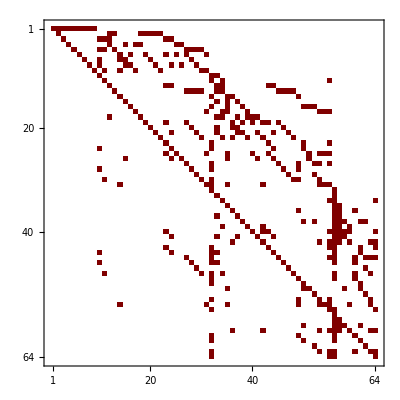

#### check flatness

```mathematica
Coefficient[Amatrix64,e];
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

#### recover A matrix in kinematic flow

```mathematica
basisKinematic={-⟨1,2,3,4⟩+⟨1,2,3,8⟩-⟨1,2,4,7⟩-⟨1,2,4,8⟩+⟨1,2,4,10⟩-⟨1,2,7,10⟩+⟨1,3,4,6⟩+⟨1,3,4,7⟩-⟨1,3,4,9⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,3,6,8⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩-⟨1,4,5,6⟩+⟨1,4,5,8⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩+⟨1,4,8,10⟩+⟨1,5,6,9⟩-⟨2,3,4,6⟩-⟨2,3,6,8⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,8⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨3,4,7,9⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨4,5,8,10⟩,-⟨2,3,4,6⟩+⟨2,3,4,11⟩-⟨2,3,6,8⟩-⟨2,3,8,11⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,8⟩+⟨2,4,6,9⟩-⟨2,4,7,9⟩+⟨2,4,7,11⟩+⟨2,4,8,11⟩-⟨2,4,10,11⟩-⟨2,5,6,9⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩+⟨2,7,10,11⟩-⟨3,4,6,11⟩+⟨3,4,7,9⟩-⟨3,4,7,11⟩+⟨3,4,9,11⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨3,6,8,11⟩-⟨3,7,10,11⟩+⟨3,8,10,11⟩+⟨4,5,6,11⟩+⟨4,5,8,10⟩-⟨4,5,8,11⟩+⟨4,6,8,11⟩+⟨4,6,9,11⟩-⟨4,8,10,11⟩-⟨5,6,9,11⟩,⟨1,2,3,8⟩-⟨1,2,3,14⟩-⟨1,2,7,10⟩+⟨1,2,7,14⟩+⟨1,2,8,14⟩-⟨1,2,10,14⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩+⟨1,3,6,8⟩-⟨1,3,6,14⟩+⟨1,3,7,10⟩-⟨1,3,7,14⟩-⟨1,3,8,10⟩+⟨1,3,9,14⟩+⟨1,5,6,9⟩-⟨1,5,6,14⟩+⟨1,5,8,14⟩-⟨1,6,8,14⟩-⟨1,6,9,14⟩+⟨1,8,10,14⟩-⟨2,3,6,8⟩+⟨2,3,6,14⟩-⟨2,5,6,9⟩+⟨2,5,6,14⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,14⟩+⟨2,6,8,14⟩+⟨2,6,9,14⟩-⟨2,7,9,14⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,7,9,14⟩-⟨5,8,10,14⟩,⟨1,3,4,6⟩-⟨1,3,4,12⟩+⟨1,3,6,8⟩+⟨1,3,8,12⟩-⟨1,4,5,6⟩+⟨1,4,5,12⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩-⟨1,4,8,12⟩-⟨1,4,9,12⟩+⟨1,5,6,9⟩+⟨1,5,9,12⟩+⟨3,4,6,12⟩+⟨3,6,8,12⟩-⟨4,5,6,12⟩-⟨4,6,8,12⟩-⟨4,6,9,12⟩+⟨5,6,9,12⟩,-⟨1,3,4,9⟩+⟨1,3,4,12⟩-⟨1,3,5,8⟩+⟨1,3,5,9⟩-⟨1,3,8,12⟩+⟨1,4,5,8⟩-⟨1,4,5,12⟩+⟨1,4,8,12⟩+⟨1,4,9,12⟩-⟨1,5,9,12⟩-⟨3,4,9,12⟩-⟨3,5,8,12⟩+⟨3,5,9,12⟩+⟨4,5,8,12⟩,⟨1,3,4,7⟩-⟨1,3,4,12⟩+⟨1,3,7,10⟩-⟨1,3,8,10⟩+⟨1,3,8,12⟩-⟨1,4,7,12⟩+⟨1,4,8,10⟩-⟨1,4,8,12⟩+⟨1,4,10,12⟩-⟨1,7,10,12⟩+⟨3,4,7,9⟩+⟨3,4,9,12⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,12⟩-⟨3,5,9,12⟩+⟨4,5,8,10⟩-⟨4,5,8,12⟩+⟨4,5,10,12⟩+⟨4,7,9,12⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩,-⟨1,2,4,7⟩+⟨1,2,4,13⟩-⟨1,2,7,10⟩-⟨1,2,10,13⟩-⟨1,4,6,9⟩+⟨1,4,6,13⟩+⟨1,4,7,13⟩-⟨1,4,9,13⟩+⟨1,5,6,9⟩-⟨1,5,6,13⟩+⟨1,5,9,13⟩+⟨1,7,10,13⟩+⟨2,4,6,9⟩-⟨2,4,6,13⟩-⟨2,4,7,9⟩-⟨2,5,6,9⟩+⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,13⟩-⟨4,7,9,13⟩+⟨5,7,9,13⟩-⟨5,7,10,13⟩,⟨1,2,4,10⟩-⟨1,2,4,13⟩+⟨1,2,10,13⟩-⟨1,4,5,6⟩+⟨1,4,5,13⟩-⟨1,4,6,13⟩-⟨1,4,10,13⟩+⟨1,5,6,13⟩+⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,13⟩-⟨2,5,6,13⟩+⟨2,5,10,13⟩-⟨4,5,10,13⟩,-⟨1,2,4,8⟩+⟨1,2,4,13⟩-⟨1,2,8,13⟩+⟨1,4,5,8⟩-⟨1,4,5,13⟩-⟨1,4,6,8⟩+⟨1,4,6,13⟩+⟨1,4,8,10⟩+⟨1,4,10,13⟩-⟨1,5,8,13⟩+⟨1,6,8,13⟩-⟨1,8,10,13⟩+⟨2,4,6,8⟩-⟨2,4,6,13⟩-⟨2,6,8,13⟩+⟨4,5,8,10⟩+⟨4,5,10,13⟩+⟨5,8,10,13⟩,-⟨2,3,6,8⟩+⟨2,3,6,14⟩-⟨2,3,8,11⟩-⟨2,3,11,14⟩-⟨2,5,6,9⟩+⟨2,5,6,14⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,14⟩+⟨2,6,8,14⟩+⟨2,6,9,14⟩-⟨2,7,9,14⟩+⟨2,7,10,11⟩+⟨2,7,11,14⟩+⟨2,8,11,14⟩-⟨2,10,11,14⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,11⟩-⟨3,5,9,11⟩-⟨3,6,8,11⟩-⟨3,6,11,14⟩+⟨3,7,9,14⟩-⟨3,7,10,11⟩-⟨3,7,11,14⟩+⟨3,8,10,11⟩+⟨3,9,11,14⟩-⟨5,6,9,11⟩-⟨5,6,11,14⟩-⟨5,8,10,14⟩+⟨5,8,11,14⟩-⟨6,8,11,14⟩-⟨6,9,11,14⟩+⟨8,10,11,14⟩,-⟨3,4,6,11⟩+⟨3,4,6,12⟩-⟨3,4,11,12⟩-⟨3,6,8,11⟩+⟨3,6,8,12⟩+⟨3,8,11,12⟩+⟨4,5,6,11⟩-⟨4,5,6,12⟩+⟨4,5,11,12⟩+⟨4,6,8,11⟩-⟨4,6,8,12⟩+⟨4,6,9,11⟩-⟨4,6,9,12⟩-⟨4,8,11,12⟩-⟨4,9,11,12⟩-⟨5,6,9,11⟩+⟨5,6,9,12⟩+⟨5,9,11,12⟩,⟨3,4,9,11⟩-⟨3,4,9,12⟩+⟨3,4,11,12⟩+⟨3,5,8,11⟩-⟨3,5,8,12⟩-⟨3,5,9,11⟩+⟨3,5,9,12⟩-⟨3,8,11,12⟩-⟨4,5,8,11⟩+⟨4,5,8,12⟩-⟨4,5,11,12⟩+⟨4,8,11,12⟩+⟨4,9,11,12⟩-⟨5,9,11,12⟩,⟨3,4,7,9⟩-⟨3,4,7,11⟩+⟨3,4,9,12⟩-⟨3,4,11,12⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,12⟩-⟨3,5,9,12⟩-⟨3,7,10,11⟩+⟨3,8,10,11⟩+⟨3,8,11,12⟩+⟨4,5,8,10⟩-⟨4,5,8,12⟩+⟨4,5,10,12⟩+⟨4,7,9,12⟩-⟨4,7,11,12⟩-⟨4,8,10,11⟩-⟨4,8,11,12⟩+⟨4,10,11,12⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩-⟨7,10,11,12⟩,⟨2,4,6,9⟩-⟨2,4,6,13⟩-⟨2,4,7,9⟩+⟨2,4,7,11⟩+⟨2,4,11,13⟩-⟨2,5,6,9⟩+⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,13⟩+⟨2,7,10,11⟩-⟨2,10,11,13⟩+⟨4,6,9,11⟩+⟨4,6,11,13⟩-⟨4,7,9,13⟩+⟨4,7,11,13⟩-⟨4,9,11,13⟩-⟨5,6,9,11⟩-⟨5,6,11,13⟩+⟨5,7,9,13⟩-⟨5,7,10,13⟩+⟨5,9,11,13⟩+⟨7,10,11,13⟩,⟨2,4,5,6⟩-⟨2,4,5,10⟩+⟨2,4,6,13⟩-⟨2,4,10,11⟩-⟨2,4,11,13⟩-⟨2,5,6,13⟩+⟨2,5,10,13⟩+⟨2,10,11,13⟩+⟨4,5,6,11⟩-⟨4,5,10,13⟩+⟨4,5,11,13⟩-⟨4,6,11,13⟩-⟨4,10,11,13⟩+⟨5,6,11,13⟩,⟨2,4,6,8⟩-⟨2,4,6,13⟩+⟨2,4,8,11⟩+⟨2,4,11,13⟩-⟨2,6,8,13⟩-⟨2,8,11,13⟩+⟨4,5,8,10⟩-⟨4,5,8,11⟩+⟨4,5,10,13⟩-⟨4,5,11,13⟩+⟨4,6,8,11⟩+⟨4,6,11,13⟩-⟨4,8,10,11⟩+⟨4,10,11,13⟩+⟨5,8,10,13⟩-⟨5,8,11,13⟩+⟨6,8,11,13⟩-⟨8,10,11,13⟩,⟨1,3,6,8⟩-⟨1,3,6,14⟩+⟨1,3,8,12⟩+⟨1,3,12,14⟩+⟨1,5,6,9⟩-⟨1,5,6,14⟩+⟨1,5,9,12⟩+⟨1,5,12,14⟩-⟨1,6,8,14⟩-⟨1,6,9,14⟩-⟨1,8,12,14⟩-⟨1,9,12,14⟩+⟨3,6,8,12⟩+⟨3,6,12,14⟩+⟨5,6,9,12⟩+⟨5,6,12,14⟩+⟨6,8,12,14⟩+⟨6,9,12,14⟩,-⟨1,4,6,9⟩+⟨1,4,6,13⟩-⟨1,4,9,12⟩-⟨1,4,12,13⟩+⟨1,5,6,9⟩-⟨1,5,6,13⟩+⟨1,5,9,12⟩+⟨1,5,12,13⟩-⟨4,6,9,12⟩-⟨4,6,12,13⟩+⟨5,6,9,12⟩+⟨5,6,12,13⟩,-⟨1,4,5,6⟩+⟨1,4,5,12⟩-⟨1,4,6,13⟩+⟨1,4,12,13⟩+⟨1,5,6,13⟩-⟨1,5,12,13⟩-⟨4,5,6,12⟩+⟨4,6,12,13⟩-⟨5,6,12,13⟩,-⟨1,4,6,8⟩+⟨1,4,6,13⟩-⟨1,4,8,12⟩-⟨1,4,12,13⟩+⟨1,6,8,13⟩+⟨1,8,12,13⟩-⟨4,6,8,12⟩-⟨4,6,12,13⟩-⟨6,8,12,13⟩,-⟨1,3,5,8⟩+⟨1,3,5,9⟩-⟨1,3,8,12⟩+⟨1,3,9,14⟩-⟨1,3,12,14⟩+⟨1,5,8,14⟩-⟨1,5,9,12⟩-⟨1,5,12,14⟩+⟨1,8,12,14⟩+⟨1,9,12,14⟩-⟨3,5,8,12⟩+⟨3,5,9,12⟩-⟨3,9,12,14⟩-⟨5,8,12,14⟩,⟨1,4,9,12⟩-⟨1,4,9,13⟩+⟨1,4,12,13⟩-⟨1,5,9,12⟩+⟨1,5,9,13⟩-⟨1,5,12,13⟩+⟨4,9,12,13⟩-⟨5,9,12,13⟩,-⟨1,4,5,12⟩+⟨1,4,5,13⟩-⟨1,4,12,13⟩+⟨1,5,12,13⟩-⟨4,5,12,13⟩,⟨1,4,5,8⟩-⟨1,4,5,13⟩+⟨1,4,8,12⟩+⟨1,4,12,13⟩-⟨1,5,8,13⟩-⟨1,8,12,13⟩+⟨4,5,8,12⟩+⟨4,5,12,13⟩+⟨5,8,12,13⟩,⟨1,3,7,10⟩-⟨1,3,7,14⟩-⟨1,3,8,10⟩+⟨1,3,8,12⟩+⟨1,3,12,14⟩-⟨1,7,10,12⟩-⟨1,7,12,14⟩+⟨1,8,10,14⟩-⟨1,8,12,14⟩+⟨1,10,12,14⟩-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,12⟩-⟨3,5,9,12⟩+⟨3,7,9,14⟩+⟨3,9,12,14⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩-⟨5,8,10,14⟩+⟨5,8,12,14⟩-⟨5,10,12,14⟩-⟨7,9,12,14⟩,-⟨1,4,7,12⟩+⟨1,4,7,13⟩-⟨1,4,12,13⟩-⟨1,7,10,12⟩+⟨1,7,10,13⟩+⟨1,10,12,13⟩+⟨4,7,9,12⟩-⟨4,7,9,13⟩-⟨4,9,12,13⟩-⟨5,7,9,12⟩+⟨5,7,9,13⟩+⟨5,7,10,12⟩-⟨5,7,10,13⟩+⟨5,9,12,13⟩-⟨5,10,12,13⟩,⟨1,4,10,12⟩-⟨1,4,10,13⟩+⟨1,4,12,13⟩-⟨1,10,12,13⟩+⟨4,5,10,12⟩-⟨4,5,10,13⟩+⟨4,5,12,13⟩+⟨5,10,12,13⟩,⟨1,4,8,10⟩-⟨1,4,8,12⟩+⟨1,4,10,13⟩-⟨1,4,12,13⟩-⟨1,8,10,13⟩+⟨1,8,12,13⟩+⟨4,5,8,10⟩-⟨4,5,8,12⟩+⟨4,5,10,13⟩-⟨4,5,12,13⟩+⟨5,8,10,13⟩-⟨5,8,12,13⟩,-⟨1,2,7,10⟩+⟨1,2,7,14⟩-⟨1,2,10,13⟩-⟨1,2,13,14⟩+⟨1,5,6,9⟩-⟨1,5,6,13⟩+⟨1,5,9,13⟩-⟨1,6,9,14⟩+⟨1,6,13,14⟩+⟨1,7,10,13⟩+⟨1,7,13,14⟩-⟨1,9,13,14⟩-⟨2,5,6,9⟩+⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,13⟩+⟨2,6,9,14⟩-⟨2,6,13,14⟩-⟨2,7,9,14⟩+⟨5,7,9,13⟩-⟨5,7,10,13⟩+⟨7,9,13,14⟩,⟨1,2,10,13⟩-⟨1,2,10,14⟩+⟨1,2,13,14⟩+⟨1,5,6,13⟩-⟨1,5,6,14⟩+⟨1,5,13,14⟩-⟨1,6,13,14⟩-⟨1,10,13,14⟩-⟨2,5,6,13⟩+⟨2,5,6,14⟩+⟨2,5,10,13⟩-⟨2,5,10,14⟩+⟨2,6,13,14⟩+⟨5,10,13,14⟩,-⟨1,2,8,13⟩+⟨1,2,8,14⟩-⟨1,2,13,14⟩-⟨1,5,8,13⟩+⟨1,5,8,14⟩-⟨1,5,13,14⟩+⟨1,6,8,13⟩-⟨1,6,8,14⟩+⟨1,6,13,14⟩-⟨1,8,10,13⟩+⟨1,8,10,14⟩+⟨1,10,13,14⟩-⟨2,6,8,13⟩+⟨2,6,8,14⟩-⟨2,6,13,14⟩+⟨5,8,10,13⟩-⟨5,8,10,14⟩-⟨5,10,13,14⟩,-⟨3,6,8,11⟩+⟨3,6,8,12⟩-⟨3,6,11,14⟩+⟨3,6,12,14⟩+⟨3,8,11,12⟩-⟨3,11,12,14⟩-⟨5,6,9,11⟩+⟨5,6,9,12⟩-⟨5,6,11,14⟩+⟨5,6,12,14⟩+⟨5,9,11,12⟩-⟨5,11,12,14⟩-⟨6,8,11,14⟩+⟨6,8,12,14⟩-⟨6,9,11,14⟩+⟨6,9,12,14⟩+⟨8,11,12,14⟩+⟨9,11,12,14⟩,⟨4,6,9,11⟩-⟨4,6,9,12⟩+⟨4,6,11,13⟩-⟨4,6,12,13⟩-⟨4,9,11,12⟩+⟨4,11,12,13⟩-⟨5,6,9,11⟩+⟨5,6,9,12⟩-⟨5,6,11,13⟩+⟨5,6,12,13⟩+⟨5,9,11,12⟩-⟨5,11,12,13⟩,⟨4,5,6,11⟩-⟨4,5,6,12⟩+⟨4,5,11,12⟩-⟨4,6,11,13⟩+⟨4,6,12,13⟩-⟨4,11,12,13⟩+⟨5,6,11,13⟩-⟨5,6,12,13⟩+⟨5,11,12,13⟩,⟨4,6,8,11⟩-⟨4,6,8,12⟩+⟨4,6,11,13⟩-⟨4,6,12,13⟩-⟨4,8,11,12⟩+⟨4,11,12,13⟩+⟨6,8,11,13⟩-⟨6,8,12,13⟩-⟨8,11,12,13⟩,⟨3,5,8,11⟩-⟨3,5,8,12⟩-⟨3,5,9,11⟩+⟨3,5,9,12⟩-⟨3,8,11,12⟩+⟨3,9,11,14⟩-⟨3,9,12,14⟩+⟨3,11,12,14⟩+⟨5,8,11,14⟩-⟨5,8,12,14⟩-⟨5,9,11,12⟩+⟨5,11,12,14⟩-⟨8,11,12,14⟩-⟨9,11,12,14⟩,⟨4,9,11,12⟩-⟨4,9,11,13⟩+⟨4,9,12,13⟩-⟨4,11,12,13⟩-⟨5,9,11,12⟩+⟨5,9,11,13⟩-⟨5,9,12,13⟩+⟨5,11,12,13⟩,-⟨4,5,11,12⟩+⟨4,5,11,13⟩-⟨4,5,12,13⟩+⟨4,11,12,13⟩-⟨5,11,12,13⟩,-⟨4,5,8,11⟩+⟨4,5,8,12⟩-⟨4,5,11,13⟩+⟨4,5,12,13⟩+⟨4,8,11,12⟩-⟨4,11,12,13⟩-⟨5,8,11,13⟩+⟨5,8,12,13⟩+⟨8,11,12,13⟩,-⟨3,5,7,9⟩+⟨3,5,7,10⟩-⟨3,5,8,10⟩+⟨3,5,8,12⟩-⟨3,5,9,12⟩+⟨3,7,9,14⟩-⟨3,7,10,11⟩-⟨3,7,11,14⟩+⟨3,8,10,11⟩+⟨3,8,11,12⟩+⟨3,9,12,14⟩-⟨3,11,12,14⟩-⟨5,7,9,12⟩+⟨5,7,10,12⟩-⟨5,8,10,14⟩+⟨5,8,12,14⟩-⟨5,10,12,14⟩-⟨7,9,12,14⟩-⟨7,10,11,12⟩+⟨7,11,12,14⟩+⟨8,10,11,14⟩+⟨8,11,12,14⟩-⟨10,11,12,14⟩,⟨4,7,9,12⟩-⟨4,7,9,13⟩-⟨4,7,11,12⟩+⟨4,7,11,13⟩-⟨4,9,12,13⟩+⟨4,11,12,13⟩-⟨5,7,9,12⟩+⟨5,7,9,13⟩+⟨5,7,10,12⟩-⟨5,7,10,13⟩+⟨5,9,12,13⟩-⟨5,10,12,13⟩-⟨7,10,11,12⟩+⟨7,10,11,13⟩-⟨10,11,12,13⟩,⟨4,5,10,12⟩-⟨4,5,10,13⟩+⟨4,5,12,13⟩+⟨4,10,11,12⟩-⟨4,10,11,13⟩-⟨4,11,12,13⟩+⟨5,10,12,13⟩+⟨10,11,12,13⟩,⟨4,5,8,10⟩-⟨4,5,8,12⟩+⟨4,5,10,13⟩-⟨4,5,12,13⟩-⟨4,8,10,11⟩-⟨4,8,11,12⟩+⟨4,10,11,13⟩+⟨4,11,12,13⟩+⟨5,8,10,13⟩-⟨5,8,12,13⟩-⟨8,10,11,13⟩-⟨8,11,12,13⟩,-⟨2,5,6,9⟩+⟨2,5,6,13⟩+⟨2,5,7,9⟩-⟨2,5,7,10⟩-⟨2,5,10,13⟩+⟨2,6,9,14⟩-⟨2,6,13,14⟩-⟨2,7,9,14⟩+⟨2,7,10,11⟩+⟨2,7,11,14⟩-⟨2,10,11,13⟩+⟨2,11,13,14⟩-⟨5,6,9,11⟩-⟨5,6,11,13⟩+⟨5,7,9,13⟩-⟨5,7,10,13⟩+⟨5,9,11,13⟩-⟨6,9,11,14⟩-⟨6,11,13,14⟩+⟨7,9,13,14⟩+⟨7,10,11,13⟩-⟨7,11,13,14⟩+⟨9,11,13,14⟩,-⟨2,5,6,13⟩+⟨2,5,6,14⟩+⟨2,5,10,13⟩-⟨2,5,10,14⟩+⟨2,6,13,14⟩+⟨2,10,11,13⟩-⟨2,10,11,14⟩-⟨2,11,13,14⟩+⟨5,6,11,13⟩-⟨5,6,11,14⟩+⟨5,10,13,14⟩-⟨5,11,13,14⟩+⟨6,11,13,14⟩+⟨10,11,13,14⟩,-⟨2,6,8,13⟩+⟨2,6,8,14⟩-⟨2,6,13,14⟩-⟨2,8,11,13⟩+⟨2,8,11,14⟩+⟨2,11,13,14⟩+⟨5,8,10,13⟩-⟨5,8,10,14⟩-⟨5,8,11,13⟩+⟨5,8,11,14⟩-⟨5,10,13,14⟩+⟨5,11,13,14⟩+⟨6,8,11,13⟩-⟨6,8,11,14⟩-⟨6,11,13,14⟩-⟨8,10,11,13⟩+⟨8,10,11,14⟩-⟨10,11,13,14⟩,⟨1,5,6,9⟩-⟨1,5,6,13⟩+⟨1,5,9,12⟩+⟨1,5,12,13⟩-⟨1,6,9,14⟩+⟨1,6,13,14⟩-⟨1,9,12,14⟩-⟨1,12,13,14⟩+⟨5,6,9,12⟩+⟨5,6,12,13⟩+⟨6,9,12,14⟩+⟨6,12,13,14⟩,⟨1,5,6,13⟩-⟨1,5,6,14⟩-⟨1,5,12,13⟩+⟨1,5,12,14⟩-⟨1,6,13,14⟩+⟨1,12,13,14⟩-⟨5,6,12,13⟩+⟨5,6,12,14⟩-⟨6,12,13,14⟩,⟨1,6,8,13⟩-⟨1,6,8,14⟩+⟨1,6,13,14⟩+⟨1,8,12,13⟩-⟨1,8,12,14⟩-⟨1,12,13,14⟩-⟨6,8,12,13⟩+⟨6,8,12,14⟩+⟨6,12,13,14⟩,-⟨1,5,9,12⟩+⟨1,5,9,13⟩-⟨1,5,12,13⟩+⟨1,9,12,14⟩-⟨1,9,13,14⟩+⟨1,12,13,14⟩-⟨5,9,12,13⟩-⟨9,12,13,14⟩,⟨1,5,12,13⟩-⟨1,5,12,14⟩+⟨1,5,13,14⟩-⟨1,12,13,14⟩+⟨5,12,13,14⟩,-⟨1,5,8,13⟩+⟨1,5,8,14⟩-⟨1,5,13,14⟩-⟨1,8,12,13⟩+⟨1,8,12,14⟩+⟨1,12,13,14⟩+⟨5,8,12,13⟩-⟨5,8,12,14⟩-⟨5,12,13,14⟩,-⟨1,7,10,12⟩+⟨1,7,10,13⟩-⟨1,7,12,14⟩+⟨1,7,13,14⟩+⟨1,10,12,13⟩-⟨1,12,13,14⟩-⟨5,7,9,12⟩+⟨5,7,9,13⟩+⟨5,7,10,12⟩-⟨5,7,10,13⟩+⟨5,9,12,13⟩-⟨5,10,12,13⟩-⟨7,9,12,14⟩+⟨7,9,13,14⟩+⟨9,12,13,14⟩,-⟨1,10,12,13⟩+⟨1,10,12,14⟩-⟨1,10,13,14⟩+⟨1,12,13,14⟩+⟨5,10,12,13⟩-⟨5,10,12,14⟩+⟨5,10,13,14⟩-⟨5,12,13,14⟩,-⟨1,8,10,13⟩+⟨1,8,10,14⟩+⟨1,8,12,13⟩-⟨1,8,12,14⟩+⟨1,10,13,14⟩-⟨1,12,13,14⟩+⟨5,8,10,13⟩-⟨5,8,10,14⟩-⟨5,8,12,13⟩+⟨5,8,12,14⟩-⟨5,10,13,14⟩+⟨5,12,13,14⟩,-⟨5,6,9,11⟩+⟨5,6,9,12⟩-⟨5,6,11,13⟩+⟨5,6,12,13⟩+⟨5,9,11,12⟩-⟨5,11,12,13⟩-⟨6,9,11,14⟩+⟨6,9,12,14⟩-⟨6,11,13,14⟩+⟨6,12,13,14⟩+⟨9,11,12,14⟩-⟨11,12,13,14⟩,⟨5,6,11,13⟩-⟨5,6,11,14⟩-⟨5,6,12,13⟩+⟨5,6,12,14⟩+⟨5,11,12,13⟩-⟨5,11,12,14⟩+⟨6,11,13,14⟩-⟨6,12,13,14⟩+⟨11,12,13,14⟩,⟨6,8,11,13⟩-⟨6,8,11,14⟩-⟨6,8,12,13⟩+⟨6,8,12,14⟩-⟨6,11,13,14⟩+⟨6,12,13,14⟩-⟨8,11,12,13⟩+⟨8,11,12,14⟩-⟨11,12,13,14⟩,-⟨5,9,11,12⟩+⟨5,9,11,13⟩-⟨5,9,12,13⟩+⟨5,11,12,13⟩-⟨9,11,12,14⟩+⟨9,11,13,14⟩-⟨9,12,13,14⟩+⟨11,12,13,14⟩,-⟨5,11,12,13⟩+⟨5,11,12,14⟩-⟨5,11,13,14⟩+⟨5,12,13,14⟩-⟨11,12,13,14⟩,-⟨5,8,11,13⟩+⟨5,8,11,14⟩+⟨5,8,12,13⟩-⟨5,8,12,14⟩+⟨5,11,13,14⟩-⟨5,12,13,14⟩+⟨8,11,12,13⟩-⟨8,11,12,14⟩+⟨11,12,13,14⟩,-⟨5,7,9,12⟩+⟨5,7,9,13⟩+⟨5,7,10,12⟩-⟨5,7,10,13⟩+⟨5,9,12,13⟩-⟨5,10,12,13⟩-⟨7,9,12,14⟩+⟨7,9,13,14⟩-⟨7,10,11,12⟩+⟨7,10,11,13⟩+⟨7,11,12,14⟩-⟨7,11,13,14⟩+⟨9,12,13,14⟩-⟨10,11,12,13⟩-⟨11,12,13,14⟩,⟨5,10,12,13⟩-⟨5,10,12,14⟩+⟨5,10,13,14⟩-⟨5,12,13,14⟩+⟨10,11,12,13⟩-⟨10,11,12,14⟩+⟨10,11,13,14⟩+⟨11,12,13,14⟩,⟨5,8,10,13⟩-⟨5,8,10,14⟩-⟨5,8,12,13⟩+⟨5,8,12,14⟩-⟨5,10,13,14⟩+⟨5,12,13,14⟩-⟨8,10,11,13⟩+⟨8,10,11,14⟩-⟨8,11,12,13⟩+⟨8,11,12,14⟩-⟨10,11,13,14⟩-⟨11,12,13,14⟩};
```

we should do a composition : 16x26 times 26x16 to obtain this 16x16 U matrix, as we need to use the 26d quotient space.

```mathematica
UmatrixK0=Table[Coefficient[basisKinematic[[i]]/.sol,basis[[j]]],{i,1,Length[basisKinematic]},{j,1,Length[basis]}];
UK0inv=Simplify[PseudoInverse[UmatrixK0]];
```

```mathematica
UmatrixK0//Dimensions
UK0inv//Dimensions
```

{64,234}

{234,64}

```mathematica
UmatrixK=UmatrixK0.Uinv;
UKinv=Simplify[Inverse[UmatrixK]];
```

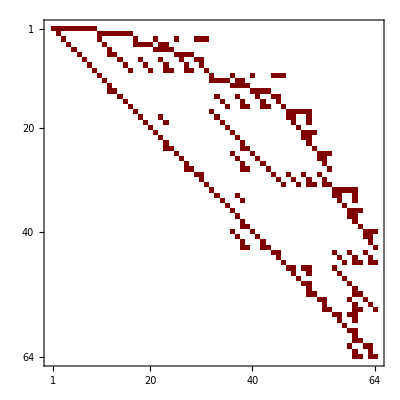

```mathematica
AmatrixK=UmatrixK.Amatrix64.UKinv//Simplify;
%//MatrixPlot
```

matches the known result:

-Graphics-